# RMT :: Bootstrap

考虑 V(A, B) = - 1/2 h[A, B]^2+1/2(A^2+B^2)+g/4(A^4+B^4) 的两矩阵模型，使用 Loop Equation(LE.) 和 Positivity Constrains 的限制后，问题可以被描述为一类半正定规划。

参考文献：
Kazakov, V., & Zheng, Z. (2022). Analytic and Numerical Bootstrap for One-Matrix Model and “Unsolvable” Two-Matrix Model. Journal of High Energy Physics, 2022(6), 30. https://doi.org/10.1007/JHEP06(2022)030

## Prefatory.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<ToCVXPY`
```

ToCVXPY beta 1.2.0

------------------

Use GenerateTask[target, allVars, sdpMatrix, loopEquations, para, lambda, eps]

to create Task.json in order to transport the SDP question into CVXPY

Parameter:

target: The coefficients of the target function.

{1, 0, 2} will give allVars[1] + 2 allVars[3] as target.

allVars: All the variables shown in this SDP problem.

sdpMatrix: SDP Matrix as constrains.

loopEquations: Equations constrains. Can include a parameter.

para: The parameter shown in loopEquations.

lambda: The discrete values of para.

eps: The threshold of the SDP algorithm. It must be in the interval [10^-9, 10^-3]

------------------

DREAM @ 20240603

## Word 处理

### Z2Sym

交换 A,B

```mathematica
ClearAll[Z2Sym]
Z2Sym[word_]:=word/.{A->B,B->A}
```

### 产生所有等价类

```mathematica
ClearAll[AllSameWord]
AllSameWord[word_]:=Module[{res,tmp,len},
len=Length[word];
res=Table[RotateRight[word,i],{i,1,len}];
tmp=Z2Sym[word];
Join[res,Table[RotateRight[tmp,i],{i,1,len}]]
]
```

```mathematica
AllSameWord[{A,B,A}]
```

{{A,A,B},{B,A,A},{A,B,A},{B,B,A},{A,B,B},{B,A,B}}

## Hash Operator Base

使用一个最笨的方法处理 Word 的 Cyclic 和 Z_2 结构 —— 对某个没有记录的 Word，给其一个唯一的 HOB Index，
将它及所有的等价 Word 赋予相同的 HOB Index 中加入到哈希表中。

用哈希表记录 Word → HOB Index

```mathematica
HOB=CreateDataStructure["HashTable"];
```

### 反向表

反向表记录 HOB Index → Word

```mathematica
HOBReverse=CreateDataStructure["HashTable"];
```

#### 注册新的单词

```mathematica
HOBReg[word_]:=Module[{},
HOBReverse["Insert",HOBReverse["Length"]+1->word];
HOBReverse["Length"]
]
```

#### 反向表查找

```mathematica
ClearAll[HOBResol]
HOBResol[index_]:=HOBReverse["Lookup",index];
```

### 更新

对给定的 Word，检测其是否在 HOB 已登录，如果有则返回其 HOB Index

```mathematica
ClearAll[HOBUpdate]
HOBUpdate[word_]:=Module[{newIndex,sameWords},
(* 已存在 *)
If[HOB["KeyExistsQ",word],Return[HOB["Lookup",word]]];
(* 不存在 
  1. 将 word 注册到反向表中
  2. 将 word 所有等价词全部加入到 HOB 中
*)
newIndex=HOBReg[word];
sameWords=AllSameWord[word];

For[i=1,i<=Length[sameWords],i++,
HOB["Insert",sameWords[[i]]->newIndex]
];
Return[newIndex]
]
```

## 内积

两个算符（Word）的内积定义为 Tr(O^†O)

### Word 连接

```mathematica
ClearAll[WordJoin]
WordJoin[o1_,o2_]:=DeleteCases[Join[Reverse[o1],o2],1]
```

```mathematica
WordJoin[{A,B,B},{A,A}]
```

{B,B,A,A,A}

### 内积表示

使用 e_Word表示 Tr[Word] 的期望值

```mathematica
ClearAll[e]
Subscript[e, {}]=1;
```

如果 Word 的某个 symbol 是奇数，则其结果为零

```mathematica
Subscript[e, x_List]:=0/;Or[OddQ[Count[x,A]],OddQ[Count[x,B]]]
```

#### EReduce

利用 LOE，将 e_Word 转化为 e_(Phase[Root[Word]]]) 的形式

```mathematica
ClearAll[EReduce]
EReduce[expr_]:=expr/.Subscript[e, word_List]:>Subscript[e, HOBUpdate[word]]
```

#### EResol

将 e_LOE[Word] 表示为 e_Word 的完整形式

```mathematica
ClearAll[EResol]
EResol[expr_]:=expr/.Subscript[e, x_?NumberQ]:>Subscript[e, HOBResol[x]]
```

### 内积

```mathematica
ClearAll[IP]
IP[o1_,o2_]:=Subscript[e, WordJoin[o1,o2]]
```

## Bootstrap. Tr(A^2)-g

取 h = 0，变动 g ∈ [0, 2] 绘制曲线

## Λ - cutoff

因为无法考虑所有长度的 Word，故仅考虑长度小于等于 Λ 的 Word，缝合出来的 Length 最大为 2Λ

```mathematica
Λ =7;
```

## 库

### 字典库

根据 cutoff，构造该 cutoff 下所有的 Word，其集合为字典

注意 Word 本身不存在 Cyclic 和 Z2 对称性

```mathematica
ClearAll[MakeDictionary]
MakeDictionary[l_]:=Module[{allPars,temp},
temp=Table[Table[A,{i,0,j}],{j,-1,l - 1}];
allPars=Flatten/@Transpose[{temp,Reverse[temp]/.A->B}];
Flatten[Permutations/@allPars,1]
]
```

```mathematica
dictionary = Table[MakeDictionary[i],{i,1,2Λ}]//Flatten[#,1]&//Sort;
%//Length
```

32766

#### Z2约化字典库

模掉 Z2 剩下的字典库

```mathematica
(*z2RedDic=DeleteDuplicates[dictionary,Z2Sym[#1]===#2&];*)
```

#### 全约化字典库

模掉了  Cyclic  和  Z2  对称性后剩下的字典库

```mathematica
redDic=HOBResol/@(DeleteDuplicates[HOBUpdate/@dictionary]);//Timing
```

{0.297886,Null}

```mathematica
redDic//Length
```

1323

### 算符库

将字典中的 word 全部变换为算符，并模掉所有在 Z_2^3 x Cyclic 下等价的算符

```mathematica
OPBASE=DeleteCases[Subscript[e, #]&/@redDic,0]//EReduce//DeleteDuplicates;
Length[%]
```

440

## Loop Equation

针对某个长度为 l 的 Word，本模型的 Loop Equation 会提供长度为 l - 1, l + 1 和 l + 3 的关联函数之间的关系。故仅需考虑 2 Λ - 3 的 Word 生成的 LE 即可。

### LE 生成器

LE 的形式为

-Graphics-

```mathematica
(*  对给定的 word 求其产生的对 Symbol M 的 LE 
---
  输出的结果中给出的是 {l.h.s, r.h.s} 的格式，对应 LE 等式的两边。
其中 r.h.s 是一个 List，因为里面可能给出二次项，这样便于后续做变量替换。
如果要复原成正确的 LE 方程，则只需写
l.h.s == Total[r.h.s]
*)
ClearAll[LEGen]
LEGen[word_List,M_]:=Module[{lhs,rhs,pos,pairs,cSym},
cSym=If[M===A,B,A];
(* 左侧很好处理，分别为 word 加上 {M} 和 {M, M, M} 即可 *)
lhs = Subscript[e, Join[word,{M}]]+g Subscript[e, Join[word,{M,M,M}]]+h(Subscript[e, Join[word,{M,cSym,cSym}]]+Subscript[e, Join[word,{cSym,cSym,M}]]-2 Subscript[e, Join[word,{cSym,M,cSym}]]);
(* 右侧，先找出 Word 中所有 M 的位置 *)
pos = Position[word,M]//Flatten;
(* cut *)
Cut[w_,p_]:={w[[1;;p-1]],w[[p+1;;]]};
pairs=Cut[word,#]&/@pos;

rhs=If[Length[pairs]==0,{0},Subscript[e, #[[1]]] Subscript[e, #[[2]]]&/@pairs];
{lhs,rhs}
]
```

### 生成本例中的所有 LE

考虑所有长度小于等于 2 Λ - 3 的 Word

```mathematica
Select[dictionary,Length[#]<=2Λ-3&];
temp=LEGen[#,A]&/@%;
```

处理出现的二次项

```mathematica
#[[2]]&/@temp//Flatten//DeleteDuplicates//EReduce//DeleteDuplicates;
Select[%,Total[Exponent[#,Variables[%]]]==2&];
quadRule=Table[%[[i]]->Subscript[β, i],{i,1,Length[%]}]
```

{e_2^2→β_1,e_2 e_6→β_2,e_2 e_8→β_3,e_2 e_9→β_4,e_2 e_14→β_5,e_6^2→β_6,e_2 e_16→β_7,e_6 e_8→β_8,e_2 e_17→β_9,e_6 e_9→β_10,e_2 e_19→β_11,e_8^2→β_12,e_8 e_9→β_13,e_9^2→β_14,e_2 e_32→β_15,e_6 e_14→β_16,e_2 e_34→β_17,e_6 e_16→β_18,e_8 e_14→β_19,e_2 e_35→β_20,e_6 e_17→β_21,e_9 e_14→β_22,e_2 e_37→β_23,e_6 e_19→β_24,e_2 e_40→β_25,e_2 e_41→β_26,e_2 e_44→β_27,e_2 e_46→β_28,e_2 e_48→β_29,e_2 e_49→β_30,e_2 e_50→β_31,e_2 e_51→β_32,e_8 e_16→β_33,e_9 e_16→β_34,e_8 e_17→β_35,e_9 e_17→β_36,e_8 e_19→β_37,e_9 e_19→β_38}

求解

```mathematica
loopEqs=DeleteCases[#[[1]]==Total[#[[2]]]&/@temp,True]//EReduce//DeleteDuplicates;
```

```mathematica
(*leqSols=Solve[loopEqs/.{h->0}/.quadRule]
%//Length*)
```

## 关联矩阵

对给定的 Word 矢量 x，给出其生成的关联矩阵

### 构造方法

```mathematica
(*构造对称矩阵的函数*)
ConstructSymmetricMatrix[upperTri_]:=Module[{n,symmetricMatrix},
n=Length[upperTri];
(*矩阵的阶数*)
symmetricMatrix=Table[0,{n},{n}];
(*初始化 n x n 的零矩阵*)
(*填充上三角部分*)
Do[symmetricMatrix[[i,j]]=upperTri[[i,j]];
symmetricMatrix[[j,i]]=upperTri[[i,j]];,{i,n},{j,i,n}];
symmetricMatrix]
```

```mathematica
ClearAll[MakeCorMatrix]
MakeCorMatrix[x_List]:= EReduce[Outer[IP,x,x,1]]//ConstructSymmetricMatrix
```

### even-odd words

```mathematica
Select[dictionary,(*Or[*)OddQ[Count[#,A]]&&EvenQ[Count[#,B]]&&Length[#]<=Λ&(*,EvenQ[Count[#,A]]&&OddQ[Count[#,B]]&&Length[#]<=Λ]&*)];
corMat1=MakeCorMatrix[%];
%//MatrixForm
```

(e_2 | e_6 | e_8 | e_9 | e_8 | e_14 | e_16 | e_17 | e_16 | e_19 | e_17 | e_16 | e_16 | e_17 | e_19 | e_17 | e_17 | e_16 | e_19 | e_17 | e_16 | e_32 | e_34 | e_35 | e_34 | e_37 | e_35 | e_34 | e_40 | e_41 | e_37 | e_35 | e_44 | e_34 | e_46 | e_44 | e_40 | e_37 | e_41 | e_37 | e_46 | e_35 | e_48 | e_49 | e_44 | e_34 | e_50 | e_48 | e_46 | e_46 | e_44 | e_40 | e_34 | e_35 | e_37 | e_41 | e_44 | e_37 | e_49 | e_48 | e_46 | e_35 | e_48 | e_51 | e_48 | e_48 | e_49 | e_44 | e_35 | e_34 | e_46 | e_48 | e_50 | e_49 | e_48 | e_46 | e_37 | e_44 | e_46 | e_44 | e_41 | e_40 | e_37 | e_35 | e_34
e_6 | e_14 | e_16 | e_17 | e_16 | e_32 | e_34 | e_35 | e_34 | e_37 | e_35 | e_34 | e_40 | e_41 | e_37 | e_35 | e_44 | e_34 | e_46 | e_44 | e_40 | e_82 | e_84 | e_85 | e_84 | e_87 | e_85 | e_84 | e_90 | e_91 | e_87 | e_85 | e_94 | e_84 | e_96 | e_97 | e_90 | e_99 | e_91 | e_87 | e_102 | e_85 | e_104 | e_105 | e_94 | e_84 | e_108 | e_109 | e_96 | e_111 | e_97 | e_90 | e_90 | e_91 | e_99 | e_91 | e_114 | e_87 | e_116 | e_117 | e_102 | e_85 | e_118 | e_119 | e_104 | e_121 | e_105 | e_94 | e_97 | e_84 | e_124 | e_125 | e_108 | e_127 | e_109 | e_96 | e_111 | e_114 | e_111 | e_97 | e_114 | e_90 | e_102 | e_94 | e_90
e_8 | e_16 | e_16 | e_17 | e_19 | e_34 | e_40 | e_44 | e_46 | e_46 | e_48 | e_50 | e_34 | e_44 | e_49 | e_48 | e_35 | e_46 | e_37 | e_41 | e_37 | e_84 | e_90 | e_94 | e_96 | e_102 | e_104 | e_108 | e_90 | e_114 | e_116 | e_118 | e_97 | e_124 | e_111 | e_114 | e_102 | e_111 | e_121 | e_130 | e_96 | e_125 | e_109 | e_127 | e_117 | e_108 | e_108 | e_125 | e_130 | e_124 | e_118 | e_108 | e_84 | e_97 | e_105 | e_117 | e_94 | e_127 | e_105 | e_121 | e_116 | e_109 | e_104 | e_119 | e_131 | e_118 | e_133 | e_125 | e_85 | e_96 | e_102 | e_117 | e_130 | e_116 | e_131 | e_130 | e_87 | e_114 | e_127 | e_121 | e_91 | e_111 | e_99 | e_91 | e_87
e_9 | e_17 | e_17 | e_19 | e_17 | e_35 | e_44 | e_49 | e_48 | e_48 | e_51 | e_48 | e_35 | e_46 | e_48 | e_49 | e_37 | e_44 | e_41 | e_37 | e_35 | e_85 | e_97 | e_105 | e_109 | e_117 | e_119 | e_125 | e_94 | e_127 | e_131 | e_133 | e_105 | e_118 | e_121 | e_116 | e_104 | e_109 | e_119 | e_131 | e_104 | e_119 | e_119 | e_131 | e_119 | e_104 | e_118 | e_133 | e_131 | e_125 | e_119 | e_109 | e_85 | e_96 | e_104 | e_116 | e_102 | e_121 | e_117 | e_130 | e_118 | e_105 | e_116 | e_131 | e_133 | e_130 | e_131 | e_127 | e_87 | e_94 | e_114 | e_127 | e_125 | e_121 | e_119 | e_117 | e_91 | e_111 | e_109 | e_105 | e_99 | e_97 | e_91 | e_87 | e_85
e_8 | e_16 | e_19 | e_17 | e_16 | e_34 | e_46 | e_48 | e_50 | e_49 | e_48 | e_46 | e_37 | e_44 | e_46 | e_44 | e_41 | e_40 | e_37 | e_35 | e_34 | e_84 | e_96 | e_104 | e_108 | e_116 | e_118 | e_124 | e_102 | e_121 | e_130 | e_125 | e_117 | e_108 | e_130 | e_118 | e_108 | e_105 | e_117 | e_127 | e_116 | e_109 | e_131 | e_133 | e_125 | e_96 | e_130 | e_131 | e_130 | e_127 | e_121 | e_111 | e_87 | e_94 | e_102 | e_114 | e_114 | e_111 | e_127 | e_125 | e_124 | e_97 | e_121 | e_119 | e_118 | e_117 | e_116 | e_114 | e_91 | e_90 | e_111 | e_109 | e_108 | e_105 | e_104 | e_102 | e_99 | e_97 | e_96 | e_94 | e_91 | e_90 | e_87 | e_85 | e_84
e_14 | e_32 | e_34 | e_35 | e_34 | e_82 | e_84 | e_85 | e_84 | e_87 | e_85 | e_84 | e_90 | e_91 | e_87 | e_85 | e_94 | e_84 | e_96 | e_97 | e_90 | e_232 | e_234 | e_235 | e_234 | e_237 | e_235 | e_234 | e_240 | e_241 | e_237 | e_235 | e_244 | e_234 | e_246 | e_247 | e_240 | e_249 | e_241 | e_237 | e_252 | e_235 | e_254 | e_255 | e_244 | e_234 | e_258 | e_259 | e_246 | e_261 | e_247 | e_240 | e_264 | e_265 | e_249 | e_241 | e_268 | e_237 | e_270 | e_271 | e_252 | e_235 | e_274 | e_275 | e_254 | e_277 | e_255 | e_244 | e_280 | e_234 | e_282 | e_283 | e_258 | e_285 | e_259 | e_246 | e_288 | e_289 | e_261 | e_247 | e_292 | e_240 | e_294 | e_280 | e_264
e_16 | e_34 | e_40 | e_44 | e_46 | e_84 | e_90 | e_94 | e_96 | e_102 | e_104 | e_108 | e_90 | e_114 | e_116 | e_118 | e_97 | e_124 | e_111 | e_114 | e_102 | e_234 | e_240 | e_244 | e_246 | e_252 | e_254 | e_258 | e_264 | e_268 | e_270 | e_274 | e_280 | e_282 | e_288 | e_292 | e_294 | e_296 | e_298 | e_302 | e_294 | e_308 | e_314 | e_318 | e_320 | e_322 | e_328 | e_332 | e_334 | e_338 | e_340 | e_328 | e_240 | e_289 | e_315 | e_344 | e_292 | e_350 | e_341 | e_358 | e_360 | e_323 | e_340 | e_368 | e_370 | e_374 | e_376 | e_378 | e_247 | e_282 | e_338 | e_382 | e_384 | e_386 | e_388 | e_390 | e_261 | e_394 | e_386 | e_374 | e_289 | e_338 | e_296 | e_268 | e_252
e_17 | e_35 | e_44 | e_49 | e_48 | e_85 | e_94 | e_105 | e_109 | e_117 | e_119 | e_125 | e_94 | e_127 | e_131 | e_133 | e_105 | e_118 | e_121 | e_116 | e_104 | e_235 | e_247 | e_255 | e_259 | e_271 | e_275 | e_283 | e_280 | e_299 | e_303 | e_309 | e_321 | e_323 | e_335 | e_341 | e_314 | e_329 | e_345 | e_351 | e_320 | e_361 | e_371 | e_377 | e_371 | e_308 | e_378 | e_389 | e_391 | e_382 | e_368 | e_332 | e_244 | e_285 | e_311 | e_353 | e_318 | e_363 | e_377 | e_400 | e_370 | e_309 | e_376 | e_405 | e_407 | e_409 | e_405 | e_389 | e_255 | e_274 | e_374 | e_409 | e_406 | e_408 | e_404 | e_402 | e_277 | e_386 | e_388 | e_376 | e_315 | e_340 | e_298 | e_270 | e_254
e_16 | e_34 | e_46 | e_48 | e_50 | e_84 | e_96 | e_109 | e_108 | e_116 | e_118 | e_124 | e_102 | e_121 | e_130 | e_125 | e_117 | e_108 | e_130 | e_118 | e_108 | e_234 | e_246 | e_254 | e_258 | e_270 | e_274 | e_282 | e_294 | e_298 | e_302 | e_308 | e_320 | e_322 | e_334 | e_340 | e_328 | e_315 | e_344 | e_350 | e_360 | e_323 | e_370 | e_376 | e_378 | e_282 | e_384 | e_388 | e_390 | e_386 | e_374 | e_338 | e_252 | e_277 | e_305 | e_347 | e_358 | e_325 | e_400 | e_402 | e_384 | e_283 | e_402 | e_404 | e_406 | e_408 | e_409 | e_382 | e_271 | e_258 | e_390 | e_406 | e_410 | e_409 | e_406 | e_384 | e_305 | e_374 | e_390 | e_378 | e_344 | e_328 | e_302 | e_274 | e_258
e_19 | e_37 | e_46 | e_48 | e_49 | e_87 | e_102 | e_117 | e_116 | e_130 | e_131 | e_130 | e_96 | e_125 | e_133 | e_131 | e_109 | e_116 | e_127 | e_117 | e_105 | e_237 | e_261 | e_277 | e_285 | e_305 | e_311 | e_325 | e_288 | e_347 | e_353 | e_363 | e_335 | e_350 | e_393 | e_358 | e_318 | e_325 | e_363 | e_395 | e_334 | e_351 | e_391 | e_400 | e_377 | e_302 | e_390 | e_402 | e_400 | e_384 | e_370 | e_334 | e_246 | e_283 | e_309 | e_351 | e_332 | e_353 | e_389 | e_402 | e_376 | e_303 | e_388 | e_404 | e_405 | e_406 | e_407 | e_391 | e_259 | e_270 | e_386 | e_408 | e_409 | e_409 | e_405 | e_400 | e_285 | e_382 | e_389 | e_377 | e_329 | e_341 | e_299 | e_271 | e_255
e_17 | e_35 | e_48 | e_51 | e_48 | e_85 | e_104 | e_119 | e_118 | e_131 | e_133 | e_118 | e_104 | e_119 | e_131 | e_119 | e_119 | e_104 | e_131 | e_119 | e_109 | e_235 | e_259 | e_275 | e_283 | e_303 | e_309 | e_323 | e_314 | e_345 | e_351 | e_361 | e_371 | e_308 | e_391 | e_368 | e_332 | e_311 | e_353 | e_363 | e_370 | e_309 | e_407 | e_405 | e_389 | e_274 | e_406 | e_404 | e_402 | e_388 | e_376 | e_340 | e_254 | e_275 | e_303 | e_345 | e_368 | e_311 | e_405 | e_404 | e_388 | e_275 | e_404 | e_411 | e_404 | e_404 | e_405 | e_368 | e_275 | e_254 | e_388 | e_404 | e_406 | e_405 | e_407 | e_370 | e_311 | e_368 | e_391 | e_371 | e_345 | e_314 | e_303 | e_275 | e_259
e_16 | e_34 | e_50 | e_48 | e_46 | e_84 | e_108 | e_125 | e_124 | e_130 | e_118 | e_108 | e_108 | e_117 | e_127 | e_109 | e_125 | e_96 | e_130 | e_121 | e_111 | e_234 | e_258 | e_274 | e_282 | e_302 | e_308 | e_322 | e_328 | e_344 | e_350 | e_323 | e_378 | e_282 | e_390 | e_374 | e_338 | e_305 | e_347 | e_325 | e_384 | e_283 | e_406 | e_409 | e_382 | e_258 | e_410 | e_406 | e_384 | e_390 | e_378 | e_328 | e_258 | e_271 | e_299 | e_329 | e_382 | e_285 | e_409 | e_408 | e_386 | e_259 | e_406 | e_404 | e_388 | e_402 | e_389 | e_332 | e_283 | e_246 | e_384 | e_402 | e_390 | e_400 | e_391 | e_334 | e_325 | e_358 | e_393 | e_335 | e_347 | e_288 | e_305 | e_277 | e_261
e_16 | e_40 | e_34 | e_35 | e_37 | e_90 | e_90 | e_94 | e_102 | e_96 | e_104 | e_108 | e_84 | e_94 | e_105 | e_104 | e_85 | e_102 | e_87 | e_91 | e_99 | e_240 | e_264 | e_280 | e_288 | e_294 | e_314 | e_328 | e_240 | e_292 | e_341 | e_340 | e_247 | e_338 | e_261 | e_289 | e_296 | e_288 | e_335 | e_334 | e_246 | e_332 | e_259 | e_285 | e_329 | e_328 | e_258 | e_283 | e_325 | e_282 | e_323 | e_322 | e_234 | e_280 | e_321 | e_320 | e_244 | e_318 | e_255 | e_277 | e_315 | e_314 | e_254 | e_275 | e_311 | e_274 | e_309 | e_308 | e_235 | e_294 | e_252 | e_271 | e_305 | e_270 | e_303 | e_302 | e_237 | e_268 | e_299 | e_298 | e_241 | e_296 | e_249 | e_265 | e_249
e_17 | e_41 | e_44 | e_46 | e_44 | e_91 | e_114 | e_127 | e_121 | e_125 | e_119 | e_117 | e_94 | e_124 | e_125 | e_127 | e_111 | e_114 | e_114 | e_102 | e_94 | e_241 | e_289 | e_315 | e_329 | e_344 | e_345 | e_347 | e_292 | e_350 | e_351 | e_353 | e_341 | e_344 | e_358 | e_360 | e_320 | e_323 | e_361 | e_363 | e_340 | e_345 | e_368 | e_370 | e_371 | e_298 | e_374 | e_376 | e_377 | e_378 | e_371 | e_335 | e_247 | e_282 | e_308 | e_350 | e_338 | e_347 | e_382 | e_384 | e_378 | e_299 | e_386 | e_388 | e_389 | e_390 | e_391 | e_393 | e_261 | e_268 | e_394 | e_386 | e_382 | e_374 | e_368 | e_358 | e_289 | e_338 | e_332 | e_318 | e_296 | e_292 | e_268 | e_252 | e_244
e_19 | e_37 | e_49 | e_48 | e_46 | e_87 | e_116 | e_131 | e_130 | e_133 | e_131 | e_127 | e_105 | e_125 | e_130 | e_117 | e_121 | e_102 | e_116 | e_104 | e_96 | e_237 | e_285 | e_311 | e_325 | e_353 | e_363 | e_350 | e_318 | e_363 | e_395 | e_351 | e_377 | e_302 | e_400 | e_370 | e_334 | e_309 | e_351 | e_353 | e_376 | e_303 | e_405 | e_407 | e_391 | e_270 | e_409 | e_405 | e_400 | e_389 | e_377 | e_341 | e_255 | e_274 | e_302 | e_344 | e_374 | e_305 | e_409 | e_406 | e_390 | e_271 | e_408 | e_404 | e_402 | e_402 | e_400 | e_358 | e_277 | e_252 | e_386 | e_388 | e_384 | e_376 | e_370 | e_360 | e_315 | e_340 | e_334 | e_320 | e_298 | e_294 | e_270 | e_254 | e_246
e_17 | e_35 | e_48 | e_49 | e_44 | e_85 | e_118 | e_133 | e_125 | e_131 | e_119 | e_109 | e_104 | e_127 | e_117 | e_105 | e_127 | e_94 | e_117 | e_105 | e_97 | e_235 | e_283 | e_309 | e_323 | e_351 | e_361 | e_308 | e_332 | e_353 | e_363 | e_309 | e_389 | e_274 | e_402 | e_376 | e_340 | e_303 | e_345 | e_311 | e_388 | e_275 | e_404 | e_405 | e_368 | e_254 | e_406 | e_407 | e_370 | e_391 | e_371 | e_314 | e_259 | e_270 | e_298 | e_315 | e_386 | e_277 | e_408 | e_409 | e_374 | e_255 | e_409 | e_405 | e_376 | e_400 | e_377 | e_318 | e_285 | e_244 | e_382 | e_389 | e_378 | e_377 | e_371 | e_320 | e_329 | e_341 | e_335 | e_321 | e_299 | e_280 | e_271 | e_255 | e_247
e_17 | e_44 | e_35 | e_37 | e_41 | e_94 | e_97 | e_105 | e_117 | e_109 | e_119 | e_125 | e_85 | e_111 | e_121 | e_127 | e_87 | e_114 | e_91 | e_99 | e_91 | e_247 | e_280 | e_321 | e_335 | e_320 | e_371 | e_378 | e_244 | e_318 | e_377 | e_376 | e_255 | e_374 | e_277 | e_315 | e_298 | e_314 | e_371 | e_370 | e_254 | e_368 | e_275 | e_311 | e_345 | e_340 | e_274 | e_309 | e_363 | e_308 | e_361 | e_323 | e_235 | e_294 | e_320 | e_360 | e_252 | e_358 | e_271 | e_305 | e_344 | e_341 | e_270 | e_303 | e_353 | e_302 | e_351 | e_350 | e_237 | e_292 | e_268 | e_299 | e_347 | e_298 | e_345 | e_344 | e_241 | e_296 | e_329 | e_315 | e_249 | e_289 | e_265 | e_249 | e_241
e_16 | e_34 | e_46 | e_44 | e_40 | e_84 | e_124 | e_118 | e_108 | e_116 | e_104 | e_96 | e_102 | e_114 | e_102 | e_94 | e_114 | e_90 | e_102 | e_94 | e_90 | e_234 | e_282 | e_308 | e_322 | e_350 | e_323 | e_282 | e_338 | e_347 | e_325 | e_283 | e_382 | e_258 | e_384 | e_378 | e_328 | e_299 | e_329 | e_285 | e_386 | e_259 | e_388 | e_389 | e_332 | e_246 | e_390 | e_391 | e_334 | e_393 | e_335 | e_288 | e_261 | e_268 | e_296 | e_289 | e_394 | e_261 | e_386 | e_382 | e_338 | e_247 | e_374 | e_368 | e_340 | e_358 | e_341 | e_292 | e_289 | e_240 | e_338 | e_332 | e_328 | e_318 | e_314 | e_294 | e_296 | e_292 | e_288 | e_280 | e_268 | e_264 | e_252 | e_244 | e_240
e_19 | e_46 | e_37 | e_41 | e_37 | e_96 | e_111 | e_121 | e_130 | e_127 | e_131 | e_130 | e_87 | e_114 | e_116 | e_117 | e_91 | e_102 | e_99 | e_91 | e_87 | e_246 | e_294 | e_320 | e_334 | e_360 | e_370 | e_384 | e_252 | e_358 | e_400 | e_402 | e_271 | e_390 | e_305 | e_344 | e_302 | e_341 | e_377 | e_400 | e_270 | e_391 | e_303 | e_353 | e_351 | e_334 | e_302 | e_351 | e_395 | e_350 | e_363 | e_325 | e_237 | e_292 | e_318 | e_358 | e_268 | e_393 | e_299 | e_347 | e_350 | e_335 | e_298 | e_345 | e_363 | e_344 | e_353 | e_347 | e_241 | e_288 | e_296 | e_329 | e_325 | e_315 | e_311 | e_305 | e_249 | e_289 | e_285 | e_277 | e_265 | e_261 | e_249 | e_241 | e_237
e_17 | e_44 | e_41 | e_37 | e_35 | e_97 | e_114 | e_116 | e_118 | e_117 | e_119 | e_121 | e_91 | e_102 | e_104 | e_105 | e_99 | e_94 | e_91 | e_87 | e_85 | e_244 | e_292 | e_318 | e_332 | e_358 | e_368 | e_382 | e_268 | e_393 | e_391 | e_389 | e_299 | e_378 | e_347 | e_350 | e_308 | e_335 | e_371 | e_377 | e_298 | e_371 | e_345 | e_363 | e_361 | e_320 | e_344 | e_353 | e_351 | e_347 | e_345 | e_329 | e_241 | e_288 | e_314 | e_341 | e_296 | e_335 | e_329 | e_325 | e_323 | e_321 | e_315 | e_311 | e_309 | e_305 | e_303 | e_299 | e_249 | e_280 | e_289 | e_285 | e_283 | e_277 | e_275 | e_271 | e_265 | e_261 | e_259 | e_255 | e_249 | e_247 | e_241 | e_237 | e_235
e_16 | e_40 | e_37 | e_35 | e_34 | e_90 | e_102 | e_104 | e_108 | e_105 | e_109 | e_111 | e_99 | e_94 | e_96 | e_97 | e_91 | e_90 | e_87 | e_85 | e_84 | e_240 | e_288 | e_314 | e_328 | e_341 | e_340 | e_338 | e_296 | e_335 | e_334 | e_332 | e_329 | e_328 | e_325 | e_323 | e_322 | e_321 | e_320 | e_318 | e_315 | e_314 | e_311 | e_309 | e_308 | e_294 | e_305 | e_303 | e_302 | e_299 | e_298 | e_296 | e_249 | e_280 | e_294 | e_292 | e_289 | e_288 | e_285 | e_283 | e_282 | e_280 | e_277 | e_275 | e_274 | e_271 | e_270 | e_268 | e_265 | e_264 | e_261 | e_259 | e_258 | e_255 | e_254 | e_252 | e_249 | e_247 | e_246 | e_244 | e_241 | e_240 | e_237 | e_235 | e_234
e_32 | e_82 | e_84 | e_85 | e_84 | e_232 | e_234 | e_235 | e_234 | e_237 | e_235 | e_234 | e_240 | e_241 | e_237 | e_235 | e_247 | e_234 | e_246 | e_244 | e_240 | e_728 | e_730 | e_731 | e_730 | e_733 | e_731 | e_730 | e_736 | e_737 | e_733 | e_731 | e_740 | e_730 | e_742 | e_743 | e_736 | e_745 | e_737 | e_733 | e_748 | e_731 | e_750 | e_751 | e_740 | e_730 | e_754 | e_755 | e_742 | e_757 | e_743 | e_736 | e_760 | e_761 | e_745 | e_737 | e_764 | e_733 | e_766 | e_767 | e_748 | e_731 | e_770 | e_771 | e_750 | e_773 | e_751 | e_740 | e_776 | e_730 | e_778 | e_779 | e_754 | e_781 | e_755 | e_742 | e_784 | e_785 | e_757 | e_743 | e_788 | e_736 | e_790 | e_791 | e_760
e_34 | e_84 | e_90 | e_97 | e_96 | e_234 | e_240 | e_247 | e_246 | e_261 | e_259 | e_258 | e_264 | e_289 | e_285 | e_283 | e_280 | e_282 | e_294 | e_292 | e_288 | e_730 | e_736 | e_740 | e_742 | e_748 | e_750 | e_754 | e_760 | e_764 | e_766 | e_770 | e_776 | e_778 | e_784 | e_788 | e_790 | e_796 | e_798 | e_802 | e_808 | e_810 | e_816 | e_820 | e_822 | e_826 | e_832 | e_836 | e_838 | e_844 | e_846 | e_850 | e_760 | e_856 | e_858 | e_862 | e_868 | e_870 | e_876 | e_880 | e_882 | e_884 | e_890 | e_894 | e_896 | e_902 | e_904 | e_908 | e_791 | e_914 | e_920 | e_924 | e_926 | e_932 | e_934 | e_938 | e_853 | e_946 | e_948 | e_952 | e_958 | e_960 | e_966 | e_868 | e_808
e_35 | e_85 | e_94 | e_105 | e_104 | e_235 | e_244 | e_255 | e_254 | e_277 | e_275 | e_274 | e_280 | e_315 | e_311 | e_309 | e_321 | e_308 | e_320 | e_318 | e_314 | e_731 | e_740 | e_751 | e_755 | e_767 | e_771 | e_779 | e_791 | e_799 | e_803 | e_811 | e_823 | e_827 | e_839 | e_847 | e_851 | e_859 | e_863 | e_871 | e_883 | e_885 | e_897 | e_905 | e_909 | e_915 | e_927 | e_935 | e_939 | e_949 | e_953 | e_961 | e_776 | e_929 | e_969 | e_975 | e_987 | e_989 | e_1001 | e_1007 | e_1011 | e_1015 | e_1027 | e_1033 | e_1037 | e_1047 | e_1051 | e_1057 | e_823 | e_884 | e_1073 | e_1079 | e_1083 | e_1091 | e_1095 | e_1101 | e_911 | e_1115 | e_1119 | e_1125 | e_1063 | e_1130 | e_980 | e_876 | e_816
e_34 | e_84 | e_96 | e_109 | e_108 | e_234 | e_246 | e_259 | e_258 | e_285 | e_283 | e_282 | e_288 | e_329 | e_325 | e_323 | e_335 | e_322 | e_334 | e_332 | e_328 | e_730 | e_742 | e_755 | e_754 | e_766 | e_770 | e_778 | e_790 | e_798 | e_802 | e_810 | e_822 | e_826 | e_838 | e_846 | e_850 | e_858 | e_862 | e_870 | e_882 | e_884 | e_896 | e_904 | e_908 | e_914 | e_926 | e_934 | e_938 | e_948 | e_952 | e_960 | e_808 | e_899 | e_968 | e_974 | e_986 | e_988 | e_1000 | e_1006 | e_1010 | e_915 | e_1026 | e_1032 | e_1036 | e_1046 | e_1050 | e_1056 | e_883 | e_826 | e_1072 | e_1078 | e_1082 | e_1090 | e_1094 | e_1100 | e_1013 | e_1114 | e_1118 | e_1124 | e_1136 | e_1066 | e_994 | e_890 | e_832
e_37 | e_87 | e_102 | e_117 | e_116 | e_237 | e_252 | e_271 | e_270 | e_305 | e_303 | e_302 | e_294 | e_344 | e_353 | e_351 | e_320 | e_350 | e_360 | e_358 | e_341 | e_733 | e_748 | e_767 | e_766 | e_805 | e_813 | e_829 | e_853 | e_865 | e_873 | e_887 | e_911 | e_917 | e_941 | e_955 | e_963 | e_971 | e_977 | e_991 | e_1013 | e_1017 | e_1039 | e_1053 | e_1059 | e_988 | e_1085 | e_1097 | e_1103 | e_1121 | e_1127 | e_1106 | e_784 | e_921 | e_1021 | e_1139 | e_1110 | e_1157 | e_1175 | e_1185 | e_1191 | e_989 | e_1207 | e_1215 | e_1221 | e_1231 | e_1237 | e_1245 | e_839 | e_870 | e_1251 | e_1259 | e_1263 | e_1271 | e_1275 | e_1283 | e_941 | e_1252 | e_1280 | e_1242 | e_1107 | e_1134 | e_984 | e_880 | e_820
e_35 | e_85 | e_104 | e_119 | e_118 | e_235 | e_254 | e_275 | e_274 | e_311 | e_309 | e_308 | e_314 | e_345 | e_363 | e_361 | e_371 | e_323 | e_370 | e_368 | e_340 | e_731 | e_750 | e_771 | e_770 | e_813 | e_811 | e_827 | e_851 | e_863 | e_871 | e_885 | e_909 | e_915 | e_939 | e_953 | e_961 | e_969 | e_975 | e_989 | e_1011 | e_1015 | e_1037 | e_1051 | e_1057 | e_884 | e_1083 | e_1095 | e_1101 | e_1119 | e_1125 | e_1130 | e_816 | e_891 | e_995 | e_1137 | e_1155 | e_1017 | e_1173 | e_1183 | e_1189 | e_885 | e_1205 | e_1213 | e_1219 | e_1229 | e_1235 | e_1194 | e_897 | e_810 | e_1249 | e_1257 | e_1261 | e_1269 | e_1273 | e_1196 | e_1039 | e_1208 | e_1288 | e_1197 | e_1144 | e_1020 | e_998 | e_894 | e_836
e_34 | e_84 | e_108 | e_125 | e_124 | e_234 | e_258 | e_283 | e_282 | e_325 | e_323 | e_322 | e_328 | e_347 | e_350 | e_308 | e_378 | e_282 | e_384 | e_382 | e_338 | e_730 | e_754 | e_779 | e_778 | e_829 | e_827 | e_826 | e_850 | e_862 | e_870 | e_884 | e_908 | e_914 | e_938 | e_952 | e_960 | e_968 | e_974 | e_988 | e_1010 | e_915 | e_1036 | e_1050 | e_1056 | e_826 | e_1082 | e_1094 | e_1100 | e_1118 | e_1124 | e_1066 | e_832 | e_877 | e_981 | e_1067 | e_1154 | e_917 | e_1172 | e_1182 | e_1188 | e_827 | e_1204 | e_1212 | e_1218 | e_1228 | e_1234 | e_1070 | e_927 | e_778 | e_1248 | e_1256 | e_1248 | e_1268 | e_1249 | e_1072 | e_1085 | e_1178 | e_1251 | e_1073 | e_1150 | e_920 | e_1004 | e_902 | e_844
e_40 | e_90 | e_90 | e_94 | e_102 | e_240 | e_264 | e_280 | e_294 | e_288 | e_314 | e_328 | e_240 | e_292 | e_318 | e_332 | e_244 | e_338 | e_252 | e_268 | e_296 | e_736 | e_760 | e_791 | e_790 | e_853 | e_851 | e_850 | e_760 | e_868 | e_876 | e_890 | e_791 | e_920 | e_853 | e_958 | e_966 | e_966 | e_980 | e_994 | e_790 | e_1020 | e_851 | e_963 | e_1062 | e_1066 | e_850 | e_961 | e_1106 | e_960 | e_1130 | e_1066 | e_736 | e_958 | e_1063 | e_1136 | e_788 | e_1134 | e_847 | e_955 | e_1131 | e_1130 | e_846 | e_953 | e_1127 | e_952 | e_1125 | e_1124 | e_743 | e_960 | e_844 | e_949 | e_1121 | e_948 | e_1119 | e_1118 | e_757 | e_946 | e_1115 | e_1114 | e_785 | e_1112 | e_841 | e_856 | e_796
e_41 | e_91 | e_114 | e_127 | e_121 | e_241 | e_268 | e_299 | e_298 | e_347 | e_345 | e_344 | e_292 | e_350 | e_363 | e_353 | e_318 | e_347 | e_358 | e_393 | e_335 | e_737 | e_764 | e_799 | e_798 | e_865 | e_863 | e_862 | e_868 | e_981 | e_995 | e_1021 | e_1063 | e_1067 | e_1107 | e_1131 | e_1062 | e_1067 | e_1137 | e_1139 | e_1136 | e_1137 | e_1144 | e_1146 | e_1147 | e_974 | e_1150 | e_1152 | e_1153 | e_1154 | e_1155 | e_1110 | e_788 | e_917 | e_1017 | e_1157 | e_1134 | e_1139 | e_1162 | e_1164 | e_1165 | e_975 | e_1168 | e_1170 | e_1171 | e_1172 | e_1173 | e_1175 | e_847 | e_862 | e_1178 | e_1180 | e_1181 | e_1182 | e_1183 | e_1185 | e_955 | e_1188 | e_1189 | e_1191 | e_1131 | e_1136 | e_986 | e_882 | e_822
e_37 | e_87 | e_116 | e_131 | e_130 | e_237 | e_270 | e_303 | e_302 | e_353 | e_351 | e_350 | e_341 | e_351 | e_395 | e_363 | e_377 | e_325 | e_400 | e_391 | e_334 | e_733 | e_766 | e_803 | e_802 | e_873 | e_871 | e_870 | e_876 | e_995 | e_991 | e_1017 | e_1059 | e_988 | e_1103 | e_1127 | e_1106 | e_1021 | e_1139 | e_1157 | e_1191 | e_989 | e_1221 | e_1237 | e_1245 | e_870 | e_1263 | e_1275 | e_1283 | e_1280 | e_1242 | e_1134 | e_820 | e_887 | e_991 | e_1139 | e_1242 | e_991 | e_1293 | e_1295 | e_1290 | e_871 | e_1297 | e_1299 | e_1292 | e_1301 | e_1293 | e_1162 | e_905 | e_802 | e_1268 | e_1305 | e_1294 | e_1307 | e_1295 | e_1164 | e_1053 | e_1200 | e_1290 | e_1165 | e_1146 | e_994 | e_1000 | e_896 | e_838
e_35 | e_85 | e_118 | e_133 | e_125 | e_235 | e_274 | e_309 | e_308 | e_363 | e_361 | e_323 | e_340 | e_353 | e_351 | e_309 | e_376 | e_283 | e_402 | e_389 | e_332 | e_731 | e_770 | e_811 | e_810 | e_887 | e_885 | e_884 | e_890 | e_1021 | e_1017 | e_1015 | e_1057 | e_884 | e_1101 | e_1125 | e_1130 | e_995 | e_1137 | e_1017 | e_1189 | e_885 | e_1219 | e_1235 | e_1194 | e_810 | e_1261 | e_1273 | e_1196 | e_1288 | e_1197 | e_1020 | e_836 | e_873 | e_977 | e_1021 | e_1280 | e_887 | e_1301 | e_1307 | e_1200 | e_811 | e_1310 | e_1311 | e_1202 | e_1296 | e_1203 | e_1024 | e_935 | e_770 | e_1256 | e_1310 | e_1204 | e_1297 | e_1205 | e_1026 | e_1097 | e_1168 | e_1207 | e_1027 | e_1152 | e_890 | e_1006 | e_904 | e_846
e_44 | e_94 | e_97 | e_105 | e_117 | e_244 | e_280 | e_321 | e_320 | e_335 | e_371 | e_378 | e_247 | e_341 | e_377 | e_389 | e_255 | e_382 | e_271 | e_299 | e_329 | e_740 | e_776 | e_823 | e_822 | e_911 | e_909 | e_908 | e_791 | e_1063 | e_1059 | e_1057 | e_823 | e_1073 | e_911 | e_1063 | e_980 | e_1062 | e_1147 | e_1165 | e_822 | e_1197 | e_909 | e_1059 | e_1147 | e_1124 | e_908 | e_1057 | e_1245 | e_1056 | e_1194 | e_1070 | e_740 | e_963 | e_1059 | e_1191 | e_820 | e_1242 | e_905 | e_1053 | e_1146 | e_1125 | e_904 | e_1051 | e_1237 | e_1050 | e_1235 | e_1234 | e_751 | e_952 | e_902 | e_1047 | e_1231 | e_1046 | e_1229 | e_1228 | e_773 | e_1044 | e_1227 | e_1226 | e_817 | e_1114 | e_899 | e_858 | e_798
e_34 | e_84 | e_124 | e_118 | e_108 | e_234 | e_282 | e_323 | e_322 | e_350 | e_308 | e_282 | e_338 | e_344 | e_302 | e_274 | e_374 | e_258 | e_390 | e_378 | e_328 | e_730 | e_778 | e_827 | e_826 | e_917 | e_915 | e_914 | e_920 | e_1067 | e_988 | e_884 | e_1073 | e_826 | e_1100 | e_1124 | e_1066 | e_981 | e_1067 | e_917 | e_1188 | e_827 | e_1218 | e_1234 | e_1070 | e_778 | e_1248 | e_1249 | e_1072 | e_1251 | e_1073 | e_920 | e_844 | e_865 | e_971 | e_921 | e_1252 | e_829 | e_1254 | e_1255 | e_1076 | e_779 | e_1256 | e_1257 | e_1078 | e_1259 | e_1079 | e_924 | e_949 | e_754 | e_1248 | e_1261 | e_1082 | e_1263 | e_1083 | e_926 | e_1121 | e_1150 | e_1085 | e_927 | e_1154 | e_832 | e_1010 | e_908 | e_850
e_46 | e_96 | e_111 | e_121 | e_130 | e_246 | e_288 | e_335 | e_334 | e_393 | e_391 | e_390 | e_261 | e_358 | e_400 | e_402 | e_277 | e_384 | e_305 | e_347 | e_325 | e_742 | e_784 | e_839 | e_838 | e_941 | e_939 | e_938 | e_853 | e_1107 | e_1103 | e_1101 | e_911 | e_1100 | e_1013 | e_1136 | e_994 | e_1131 | e_1146 | e_1164 | e_882 | e_1196 | e_1011 | e_1191 | e_1165 | e_1100 | e_1010 | e_1189 | e_1290 | e_1188 | e_1200 | e_1076 | e_748 | e_955 | e_1053 | e_1185 | e_880 | e_1283 | e_1007 | e_1185 | e_1164 | e_1101 | e_1006 | e_1183 | e_1295 | e_1182 | e_1307 | e_1255 | e_767 | e_938 | e_1004 | e_1181 | e_1294 | e_1180 | e_1305 | e_1304 | e_805 | e_1178 | e_1268 | e_1228 | e_877 | e_1118 | e_968 | e_862 | e_802
e_44 | e_97 | e_114 | e_116 | e_118 | e_247 | e_292 | e_341 | e_340 | e_358 | e_368 | e_374 | e_289 | e_360 | e_370 | e_376 | e_315 | e_378 | e_344 | e_350 | e_323 | e_743 | e_788 | e_847 | e_846 | e_955 | e_953 | e_952 | e_958 | e_1131 | e_1127 | e_1125 | e_1063 | e_1124 | e_1136 | e_1134 | e_1020 | e_1107 | e_1144 | e_1162 | e_986 | e_1194 | e_1155 | e_1242 | e_1197 | e_1056 | e_1154 | e_1280 | e_1288 | e_1252 | e_1208 | e_1088 | e_764 | e_941 | e_1039 | e_1175 | e_984 | e_1245 | e_1153 | e_1283 | e_1196 | e_1057 | e_1152 | e_1275 | e_1273 | e_1271 | e_1269 | e_1267 | e_799 | e_908 | e_1150 | e_1263 | e_1261 | e_1259 | e_1257 | e_1255 | e_865 | e_1251 | e_1249 | e_1234 | e_981 | e_1124 | e_974 | e_870 | e_810
e_40 | e_90 | e_102 | e_104 | e_108 | e_240 | e_294 | e_314 | e_328 | e_318 | e_332 | e_338 | e_296 | e_320 | e_334 | e_340 | e_298 | e_328 | e_302 | e_308 | e_322 | e_736 | e_790 | e_851 | e_850 | e_963 | e_961 | e_960 | e_966 | e_1062 | e_1106 | e_1130 | e_980 | e_1066 | e_994 | e_1020 | e_1066 | e_1063 | e_1136 | e_1134 | e_1131 | e_1130 | e_1127 | e_1125 | e_1124 | e_960 | e_1121 | e_1119 | e_1118 | e_1115 | e_1114 | e_1112 | e_796 | e_911 | e_1013 | e_1110 | e_1107 | e_1106 | e_1103 | e_1101 | e_1100 | e_961 | e_1097 | e_1095 | e_1094 | e_1091 | e_1090 | e_1088 | e_859 | e_850 | e_1085 | e_1083 | e_1082 | e_1079 | e_1078 | e_1076 | e_971 | e_1073 | e_1072 | e_1070 | e_1067 | e_1066 | e_988 | e_884 | e_826
e_37 | e_99 | e_111 | e_109 | e_105 | e_249 | e_296 | e_329 | e_315 | e_325 | e_311 | e_305 | e_288 | e_323 | e_309 | e_303 | e_314 | e_299 | e_341 | e_335 | e_321 | e_745 | e_796 | e_859 | e_858 | e_971 | e_969 | e_968 | e_966 | e_1067 | e_1021 | e_995 | e_1062 | e_981 | e_1131 | e_1107 | e_1063 | e_988 | e_989 | e_991 | e_994 | e_995 | e_998 | e_1000 | e_1001 | e_968 | e_1004 | e_1006 | e_1007 | e_1010 | e_1011 | e_1013 | e_790 | e_915 | e_1015 | e_1017 | e_1020 | e_1021 | e_1024 | e_1026 | e_1027 | e_969 | e_1030 | e_1032 | e_1033 | e_1036 | e_1037 | e_1039 | e_851 | e_858 | e_1044 | e_1046 | e_1047 | e_1050 | e_1051 | e_1053 | e_963 | e_1056 | e_1057 | e_1059 | e_1062 | e_1063 | e_987 | e_883 | e_823
e_41 | e_91 | e_121 | e_119 | e_117 | e_241 | e_298 | e_345 | e_344 | e_363 | e_353 | e_347 | e_335 | e_361 | e_351 | e_345 | e_371 | e_329 | e_377 | e_371 | e_320 | e_737 | e_798 | e_863 | e_862 | e_977 | e_975 | e_974 | e_980 | e_1137 | e_1139 | e_1137 | e_1147 | e_1067 | e_1146 | e_1144 | e_1136 | e_989 | e_1157 | e_1139 | e_1165 | e_975 | e_1171 | e_1173 | e_1175 | e_862 | e_1181 | e_1183 | e_1185 | e_1189 | e_1191 | e_1136 | e_822 | e_885 | e_989 | e_1137 | e_1197 | e_977 | e_1203 | e_1205 | e_1207 | e_863 | e_1211 | e_1213 | e_1215 | e_1219 | e_1221 | e_1144 | e_909 | e_798 | e_1227 | e_1229 | e_1231 | e_1235 | e_1237 | e_1146 | e_1059 | e_1194 | e_1245 | e_1147 | e_1147 | e_980 | e_1001 | e_897 | e_839
e_37 | e_87 | e_130 | e_131 | e_127 | e_237 | e_302 | e_351 | e_350 | e_395 | e_363 | e_325 | e_334 | e_363 | e_353 | e_311 | e_370 | e_285 | e_400 | e_377 | e_318 | e_733 | e_802 | e_871 | e_870 | e_991 | e_989 | e_988 | e_994 | e_1139 | e_1157 | e_1017 | e_1165 | e_917 | e_1164 | e_1162 | e_1134 | e_991 | e_1139 | e_991 | e_1290 | e_871 | e_1292 | e_1293 | e_1162 | e_802 | e_1294 | e_1295 | e_1164 | e_1290 | e_1165 | e_994 | e_838 | e_871 | e_975 | e_995 | e_1288 | e_873 | e_1296 | e_1297 | e_1168 | e_803 | e_1298 | e_1299 | e_1170 | e_1292 | e_1171 | e_998 | e_939 | e_766 | e_1254 | e_1301 | e_1172 | e_1293 | e_1173 | e_1000 | e_1103 | e_1162 | e_1175 | e_1001 | e_1153 | e_876 | e_1007 | e_905 | e_847
e_46 | e_102 | e_96 | e_104 | e_116 | e_252 | e_294 | e_320 | e_360 | e_334 | e_370 | e_384 | e_246 | e_340 | e_376 | e_388 | e_254 | e_386 | e_270 | e_298 | e_315 | e_748 | e_808 | e_883 | e_882 | e_1013 | e_1011 | e_1010 | e_790 | e_1136 | e_1191 | e_1189 | e_822 | e_1188 | e_882 | e_986 | e_1131 | e_994 | e_1165 | e_1290 | e_838 | e_1288 | e_939 | e_1103 | e_1153 | e_1118 | e_938 | e_1101 | e_1283 | e_1100 | e_1196 | e_1072 | e_742 | e_961 | e_1057 | e_1189 | e_836 | e_1280 | e_935 | e_1097 | e_1152 | e_1119 | e_934 | e_1095 | e_1275 | e_1094 | e_1273 | e_1249 | e_755 | e_948 | e_932 | e_1091 | e_1271 | e_1090 | e_1269 | e_1268 | e_781 | e_1088 | e_1267 | e_1227 | e_833 | e_1115 | e_929 | e_859 | e_799
e_35 | e_85 | e_125 | e_119 | e_109 | e_235 | e_308 | e_361 | e_323 | e_351 | e_309 | e_283 | e_332 | e_345 | e_303 | e_275 | e_368 | e_259 | e_391 | e_371 | e_314 | e_731 | e_810 | e_885 | e_884 | e_1017 | e_1015 | e_915 | e_1020 | e_1137 | e_989 | e_885 | e_1197 | e_827 | e_1196 | e_1194 | e_1130 | e_995 | e_975 | e_871 | e_1288 | e_811 | e_1202 | e_1203 | e_1024 | e_770 | e_1204 | e_1205 | e_1026 | e_1207 | e_1027 | e_890 | e_846 | e_863 | e_969 | e_891 | e_1208 | e_813 | e_1210 | e_1211 | e_1030 | e_771 | e_1212 | e_1213 | e_1032 | e_1215 | e_1033 | e_894 | e_953 | e_750 | e_1218 | e_1219 | e_1036 | e_1221 | e_1037 | e_896 | e_1127 | e_1144 | e_1039 | e_897 | e_1155 | e_816 | e_1011 | e_909 | e_851
e_48 | e_104 | e_109 | e_119 | e_131 | e_254 | e_314 | e_371 | e_370 | e_391 | e_407 | e_406 | e_259 | e_368 | e_405 | e_404 | e_275 | e_388 | e_303 | e_345 | e_311 | e_750 | e_816 | e_897 | e_896 | e_1039 | e_1037 | e_1036 | e_851 | e_1144 | e_1221 | e_1219 | e_909 | e_1218 | e_1011 | e_1155 | e_1127 | e_998 | e_1171 | e_1292 | e_939 | e_1202 | e_1037 | e_1221 | e_1171 | e_1094 | e_1036 | e_1219 | e_1292 | e_1218 | e_1202 | e_1078 | e_750 | e_953 | e_1051 | e_1183 | e_894 | e_1275 | e_1033 | e_1215 | e_1170 | e_1095 | e_1032 | e_1213 | e_1299 | e_1212 | e_1311 | e_1257 | e_771 | e_934 | e_1030 | e_1211 | e_1298 | e_1210 | e_1313 | e_1305 | e_813 | e_1208 | e_1269 | e_1229 | e_891 | e_1119 | e_969 | e_863 | e_803
e_49 | e_105 | e_127 | e_131 | e_133 | e_255 | e_318 | e_377 | e_376 | e_400 | e_405 | e_409 | e_285 | e_370 | e_407 | e_405 | e_311 | e_389 | e_353 | e_363 | e_309 | e_751 | e_820 | e_905 | e_904 | e_1053 | e_1051 | e_1050 | e_963 | e_1146 | e_1237 | e_1235 | e_1059 | e_1234 | e_1191 | e_1242 | e_1125 | e_1000 | e_1173 | e_1293 | e_1103 | e_1203 | e_1221 | e_1293 | e_1203 | e_1050 | e_1172 | e_1301 | e_1296 | e_1254 | e_1210 | e_1090 | e_766 | e_939 | e_1037 | e_1173 | e_998 | e_1237 | e_1171 | e_1292 | e_1202 | e_1051 | e_1170 | e_1299 | e_1311 | e_1298 | e_1313 | e_1269 | e_803 | e_904 | e_1168 | e_1297 | e_1310 | e_1296 | e_1311 | e_1307 | e_873 | e_1288 | e_1273 | e_1235 | e_995 | e_1125 | e_975 | e_871 | e_811
e_44 | e_94 | e_117 | e_119 | e_125 | e_244 | e_320 | e_371 | e_378 | e_377 | e_389 | e_382 | e_329 | e_371 | e_391 | e_368 | e_345 | e_332 | e_351 | e_361 | e_308 | e_740 | e_822 | e_909 | e_908 | e_1059 | e_1057 | e_1056 | e_1062 | e_1147 | e_1245 | e_1194 | e_1147 | e_1070 | e_1165 | e_1197 | e_1124 | e_1001 | e_1175 | e_1162 | e_1153 | e_1024 | e_1171 | e_1203 | e_1234 | e_952 | e_1231 | e_1229 | e_1228 | e_1227 | e_1226 | e_1114 | e_798 | e_909 | e_1011 | e_1155 | e_1144 | e_1127 | e_1221 | e_1219 | e_1218 | e_953 | e_1215 | e_1213 | e_1212 | e_1211 | e_1210 | e_1208 | e_863 | e_846 | e_1207 | e_1205 | e_1204 | e_1203 | e_1202 | e_1200 | e_977 | e_1197 | e_1196 | e_1194 | e_1137 | e_1130 | e_989 | e_885 | e_827
e_34 | e_84 | e_108 | e_104 | e_96 | e_234 | e_322 | e_308 | e_282 | e_302 | e_274 | e_258 | e_328 | e_298 | e_270 | e_254 | e_340 | e_246 | e_334 | e_320 | e_294 | e_730 | e_826 | e_915 | e_914 | e_988 | e_884 | e_826 | e_1066 | e_974 | e_870 | e_810 | e_1124 | e_778 | e_1100 | e_1056 | e_960 | e_968 | e_862 | e_802 | e_1118 | e_770 | e_1094 | e_1050 | e_952 | e_754 | e_1082 | e_1083 | e_926 | e_1085 | e_927 | e_832 | e_850 | e_859 | e_929 | e_833 | e_1088 | e_781 | e_1090 | e_1091 | e_932 | e_755 | e_1094 | e_1095 | e_934 | e_1097 | e_935 | e_836 | e_961 | e_742 | e_1100 | e_1101 | e_938 | e_1103 | e_939 | e_838 | e_1106 | e_1107 | e_941 | e_839 | e_1110 | e_784 | e_1013 | e_911 | e_853
e_50 | e_108 | e_108 | e_118 | e_130 | e_258 | e_328 | e_378 | e_384 | e_390 | e_406 | e_410 | e_258 | e_374 | e_409 | e_406 | e_274 | e_390 | e_302 | e_344 | e_305 | e_754 | e_832 | e_927 | e_926 | e_1085 | e_1083 | e_1082 | e_850 | e_1150 | e_1263 | e_1261 | e_908 | e_1248 | e_1010 | e_1154 | e_1121 | e_1004 | e_1181 | e_1294 | e_938 | e_1204 | e_1036 | e_1172 | e_1231 | e_1082 | e_1082 | e_1261 | e_1294 | e_1248 | e_1204 | e_1082 | e_754 | e_949 | e_1047 | e_1181 | e_924 | e_1263 | e_1079 | e_1259 | e_1180 | e_1083 | e_1078 | e_1257 | e_1305 | e_1256 | e_1310 | e_1261 | e_779 | e_926 | e_1076 | e_1255 | e_1304 | e_1254 | e_1298 | e_1294 | e_829 | e_1252 | e_1271 | e_1231 | e_921 | e_1121 | e_971 | e_865 | e_805
e_48 | e_109 | e_125 | e_133 | e_131 | e_259 | e_332 | e_389 | e_388 | e_402 | e_404 | e_406 | e_283 | e_376 | e_405 | e_407 | e_309 | e_391 | e_351 | e_353 | e_303 | e_755 | e_836 | e_935 | e_934 | e_1097 | e_1095 | e_1094 | e_961 | e_1152 | e_1275 | e_1273 | e_1057 | e_1249 | e_1189 | e_1280 | e_1119 | e_1006 | e_1183 | e_1295 | e_1101 | e_1205 | e_1219 | e_1301 | e_1229 | e_1083 | e_1261 | e_1310 | e_1298 | e_1256 | e_1212 | e_1094 | e_770 | e_935 | e_1033 | e_1171 | e_1024 | e_1221 | e_1203 | e_1296 | e_1210 | e_1037 | e_1202 | e_1311 | e_1313 | e_1310 | e_1311 | e_1273 | e_811 | e_896 | e_1200 | e_1307 | e_1305 | e_1301 | e_1299 | e_1295 | e_887 | e_1280 | e_1275 | e_1237 | e_1021 | e_1127 | e_977 | e_873 | e_813
e_46 | e_96 | e_130 | e_131 | e_130 | e_246 | e_334 | e_391 | e_390 | e_400 | e_402 | e_384 | e_325 | e_377 | e_400 | e_370 | e_363 | e_334 | e_395 | e_351 | e_302 | e_742 | e_838 | e_939 | e_938 | e_1103 | e_1101 | e_1100 | e_1106 | e_1153 | e_1283 | e_1196 | e_1245 | e_1072 | e_1290 | e_1288 | e_1118 | e_1007 | e_1185 | e_1164 | e_1283 | e_1026 | e_1292 | e_1296 | e_1228 | e_926 | e_1294 | e_1298 | e_1304 | e_1268 | e_1228 | e_1118 | e_802 | e_905 | e_1007 | e_1153 | e_1162 | e_1103 | e_1293 | e_1301 | e_1254 | e_939 | e_1292 | e_1299 | e_1298 | e_1297 | e_1296 | e_1288 | e_871 | e_838 | e_1290 | e_1295 | e_1294 | e_1293 | e_1292 | e_1290 | e_991 | e_1242 | e_1283 | e_1245 | e_1139 | e_1106 | e_991 | e_887 | e_829
e_46 | e_111 | e_124 | e_125 | e_127 | e_261 | e_338 | e_382 | e_386 | e_384 | e_388 | e_390 | e_282 | e_378 | e_389 | e_391 | e_308 | e_393 | e_350 | e_347 | e_299 | e_757 | e_844 | e_949 | e_948 | e_1121 | e_1119 | e_1118 | e_960 | e_1154 | e_1280 | e_1288 | e_1056 | e_1251 | e_1188 | e_1252 | e_1115 | e_1010 | e_1189 | e_1290 | e_1100 | e_1207 | e_1218 | e_1254 | e_1227 | e_1085 | e_1248 | e_1256 | e_1268 | e_1248 | e_1218 | e_1100 | e_778 | e_927 | e_1027 | e_1165 | e_1070 | e_1191 | e_1234 | e_1228 | e_1226 | e_1011 | e_1218 | e_1212 | e_1210 | e_1204 | e_1202 | e_1196 | e_827 | e_882 | e_1188 | e_1182 | e_1180 | e_1172 | e_1170 | e_1164 | e_917 | e_1154 | e_1152 | e_1146 | e_1067 | e_1131 | e_981 | e_877 | e_817
e_44 | e_97 | e_118 | e_119 | e_121 | e_247 | e_340 | e_368 | e_374 | e_370 | e_376 | e_378 | e_323 | e_371 | e_377 | e_371 | e_361 | e_335 | e_363 | e_345 | e_298 | e_743 | e_846 | e_953 | e_952 | e_1127 | e_1125 | e_1124 | e_1130 | e_1155 | e_1242 | e_1197 | e_1194 | e_1073 | e_1200 | e_1208 | e_1114 | e_1011 | e_1191 | e_1165 | e_1196 | e_1027 | e_1202 | e_1210 | e_1226 | e_927 | e_1204 | e_1212 | e_1228 | e_1218 | e_1234 | e_1124 | e_810 | e_897 | e_1001 | e_1147 | e_1194 | e_1059 | e_1235 | e_1229 | e_1227 | e_909 | e_1219 | e_1213 | e_1211 | e_1205 | e_1203 | e_1197 | e_885 | e_822 | e_1189 | e_1183 | e_1181 | e_1173 | e_1171 | e_1165 | e_1017 | e_1155 | e_1153 | e_1147 | e_1137 | e_1062 | e_995 | e_891 | e_833
e_40 | e_90 | e_108 | e_109 | e_111 | e_240 | e_328 | e_332 | e_338 | e_334 | e_340 | e_328 | e_322 | e_335 | e_341 | e_314 | e_323 | e_288 | e_325 | e_329 | e_296 | e_736 | e_850 | e_961 | e_960 | e_1106 | e_1130 | e_1066 | e_1066 | e_1110 | e_1134 | e_1020 | e_1070 | e_920 | e_1076 | e_1088 | e_1112 | e_1013 | e_1136 | e_994 | e_1072 | e_890 | e_1078 | e_1090 | e_1114 | e_832 | e_1082 | e_1094 | e_1118 | e_1100 | e_1124 | e_1066 | e_826 | e_883 | e_987 | e_1062 | e_1056 | e_963 | e_1050 | e_1046 | e_1044 | e_851 | e_1036 | e_1032 | e_1030 | e_1026 | e_1024 | e_1020 | e_915 | e_790 | e_1010 | e_1006 | e_1004 | e_1000 | e_998 | e_994 | e_988 | e_986 | e_984 | e_980 | e_974 | e_966 | e_968 | e_899 | e_841
e_34 | e_90 | e_84 | e_85 | e_87 | e_264 | e_240 | e_244 | e_252 | e_246 | e_254 | e_258 | e_234 | e_247 | e_255 | e_259 | e_235 | e_261 | e_237 | e_241 | e_249 | e_760 | e_760 | e_776 | e_808 | e_784 | e_816 | e_832 | e_736 | e_788 | e_820 | e_836 | e_740 | e_844 | e_748 | e_764 | e_796 | e_790 | e_822 | e_838 | e_742 | e_846 | e_750 | e_766 | e_798 | e_850 | e_754 | e_770 | e_802 | e_778 | e_810 | e_826 | e_730 | e_776 | e_823 | e_822 | e_740 | e_820 | e_751 | e_773 | e_817 | e_816 | e_750 | e_771 | e_813 | e_770 | e_811 | e_810 | e_731 | e_808 | e_748 | e_767 | e_805 | e_766 | e_803 | e_802 | e_733 | e_764 | e_799 | e_798 | e_737 | e_796 | e_745 | e_761 | e_793
e_35 | e_91 | e_97 | e_96 | e_94 | e_265 | e_289 | e_285 | e_277 | e_283 | e_275 | e_271 | e_280 | e_282 | e_274 | e_270 | e_294 | e_268 | e_292 | e_288 | e_280 | e_761 | e_856 | e_929 | e_899 | e_921 | e_891 | e_877 | e_958 | e_917 | e_887 | e_873 | e_963 | e_865 | e_955 | e_941 | e_911 | e_915 | e_885 | e_871 | e_961 | e_863 | e_953 | e_939 | e_909 | e_859 | e_949 | e_935 | e_905 | e_927 | e_897 | e_883 | e_776 | e_914 | e_915 | e_917 | e_920 | e_921 | e_924 | e_926 | e_927 | e_929 | e_932 | e_934 | e_935 | e_938 | e_939 | e_941 | e_853 | e_856 | e_946 | e_948 | e_949 | e_952 | e_953 | e_955 | e_958 | e_960 | e_961 | e_963 | e_966 | e_958 | e_868 | e_808 | e_776
e_37 | e_99 | e_105 | e_104 | e_102 | e_249 | e_315 | e_311 | e_305 | e_309 | e_303 | e_299 | e_321 | e_308 | e_302 | e_298 | e_320 | e_296 | e_318 | e_314 | e_294 | e_745 | e_858 | e_969 | e_968 | e_1021 | e_995 | e_981 | e_1063 | e_1017 | e_991 | e_977 | e_1059 | e_971 | e_1053 | e_1039 | e_1013 | e_1015 | e_989 | e_975 | e_1057 | e_969 | e_1051 | e_1037 | e_1011 | e_929 | e_1047 | e_1033 | e_1007 | e_1027 | e_1001 | e_987 | e_823 | e_915 | e_988 | e_1067 | e_1073 | e_971 | e_1079 | e_1083 | e_1085 | e_859 | e_1091 | e_1095 | e_1097 | e_1101 | e_1103 | e_1107 | e_911 | e_796 | e_1115 | e_1119 | e_1121 | e_1125 | e_1127 | e_1131 | e_1063 | e_1130 | e_1106 | e_1062 | e_980 | e_966 | e_876 | e_816 | e_784
e_41 | e_91 | e_117 | e_116 | e_114 | e_241 | e_344 | e_353 | e_347 | e_351 | e_345 | e_329 | e_320 | e_350 | e_344 | e_315 | e_360 | e_289 | e_358 | e_341 | e_292 | e_737 | e_862 | e_975 | e_974 | e_1139 | e_1137 | e_1067 | e_1136 | e_1157 | e_1139 | e_1021 | e_1191 | e_921 | e_1185 | e_1175 | e_1110 | e_1017 | e_1137 | e_995 | e_1189 | e_891 | e_1183 | e_1173 | e_1155 | e_833 | e_1181 | e_1171 | e_1153 | e_1165 | e_1147 | e_1062 | e_822 | e_917 | e_1067 | e_981 | e_1251 | e_865 | e_1259 | e_1263 | e_1150 | e_799 | e_1271 | e_1275 | e_1152 | e_1283 | e_1153 | e_984 | e_941 | e_764 | e_1252 | e_1280 | e_1154 | e_1242 | e_1155 | e_986 | e_1107 | e_1134 | e_1110 | e_987 | e_984 | e_868 | e_880 | e_820 | e_788
e_44 | e_114 | e_94 | e_102 | e_114 | e_268 | e_292 | e_318 | e_358 | e_332 | e_368 | e_382 | e_244 | e_338 | e_374 | e_386 | e_252 | e_394 | e_268 | e_296 | e_289 | e_764 | e_868 | e_987 | e_986 | e_1110 | e_1155 | e_1154 | e_788 | e_1134 | e_1242 | e_1280 | e_820 | e_1252 | e_880 | e_984 | e_1107 | e_1020 | e_1197 | e_1288 | e_836 | e_1208 | e_894 | e_998 | e_1144 | e_1088 | e_924 | e_1024 | e_1162 | e_1070 | e_1194 | e_1056 | e_740 | e_920 | e_1073 | e_1251 | e_844 | e_1252 | e_949 | e_1121 | e_1154 | e_1115 | e_948 | e_1119 | e_1280 | e_1118 | e_1288 | e_1251 | e_757 | e_946 | e_946 | e_1115 | e_1252 | e_1114 | e_1208 | e_1178 | e_785 | e_1112 | e_1088 | e_1044 | e_841 | e_946 | e_856 | e_796 | e_764
e_37 | e_87 | e_127 | e_121 | e_111 | e_237 | e_350 | e_363 | e_325 | e_353 | e_311 | e_285 | e_318 | e_347 | e_305 | e_277 | e_358 | e_261 | e_393 | e_335 | e_288 | e_733 | e_870 | e_989 | e_988 | e_1157 | e_1017 | e_917 | e_1134 | e_1139 | e_991 | e_887 | e_1242 | e_829 | e_1283 | e_1245 | e_1106 | e_1021 | e_977 | e_873 | e_1280 | e_813 | e_1275 | e_1237 | e_1127 | e_781 | e_1263 | e_1221 | e_1103 | e_1191 | e_1059 | e_963 | e_820 | e_921 | e_971 | e_865 | e_1252 | e_805 | e_1180 | e_1181 | e_1004 | e_767 | e_1182 | e_1183 | e_1006 | e_1185 | e_1007 | e_880 | e_955 | e_748 | e_1188 | e_1189 | e_1010 | e_1191 | e_1011 | e_882 | e_1131 | e_1136 | e_1013 | e_883 | e_986 | e_808 | e_882 | e_822 | e_790
e_49 | e_116 | e_105 | e_117 | e_127 | e_270 | e_341 | e_377 | e_400 | e_389 | e_405 | e_409 | e_255 | e_382 | e_409 | e_408 | e_271 | e_386 | e_299 | e_329 | e_285 | e_766 | e_876 | e_1001 | e_1000 | e_1175 | e_1173 | e_1172 | e_847 | e_1162 | e_1293 | e_1301 | e_905 | e_1254 | e_1007 | e_1153 | e_1103 | e_1024 | e_1203 | e_1296 | e_935 | e_1210 | e_1033 | e_1171 | e_1221 | e_1090 | e_1079 | e_1203 | e_1293 | e_1234 | e_1235 | e_1050 | e_751 | e_924 | e_1079 | e_1259 | e_949 | e_1180 | e_1047 | e_1231 | e_1172 | e_1091 | e_1046 | e_1229 | e_1301 | e_1228 | e_1296 | e_1259 | e_773 | e_932 | e_1044 | e_1227 | e_1254 | e_1226 | e_1210 | e_1180 | e_817 | e_1114 | e_1090 | e_1046 | e_899 | e_948 | e_858 | e_798 | e_766
e_48 | e_117 | e_121 | e_130 | e_125 | e_271 | e_358 | e_400 | e_402 | e_402 | e_404 | e_408 | e_277 | e_384 | e_406 | e_409 | e_305 | e_382 | e_347 | e_325 | e_283 | e_767 | e_880 | e_1007 | e_1006 | e_1185 | e_1183 | e_1182 | e_955 | e_1164 | e_1295 | e_1307 | e_1053 | e_1255 | e_1185 | e_1283 | e_1101 | e_1026 | e_1205 | e_1297 | e_1097 | e_1211 | e_1215 | e_1292 | e_1219 | e_1091 | e_1259 | e_1296 | e_1301 | e_1228 | e_1229 | e_1046 | e_773 | e_926 | e_1083 | e_1263 | e_1121 | e_1181 | e_1231 | e_1294 | e_1204 | e_1047 | e_1180 | e_1305 | e_1310 | e_1304 | e_1298 | e_1271 | e_805 | e_902 | e_1178 | e_1268 | e_1256 | e_1228 | e_1212 | e_1182 | e_877 | e_1118 | e_1094 | e_1050 | e_968 | e_952 | e_862 | e_802 | e_770
e_46 | e_102 | e_116 | e_118 | e_124 | e_252 | e_360 | e_370 | e_384 | e_376 | e_388 | e_386 | e_315 | e_378 | e_390 | e_374 | e_344 | e_338 | e_350 | e_323 | e_282 | e_748 | e_882 | e_1011 | e_1010 | e_1191 | e_1189 | e_1188 | e_1131 | e_1165 | e_1290 | e_1200 | e_1146 | e_1076 | e_1164 | e_1196 | e_1100 | e_1027 | e_1207 | e_1168 | e_1152 | e_1030 | e_1170 | e_1202 | e_1218 | e_932 | e_1180 | e_1210 | e_1254 | e_1226 | e_1227 | e_1044 | e_817 | e_927 | e_1085 | e_1150 | e_1154 | e_1004 | e_1172 | e_1204 | e_1248 | e_949 | e_1259 | e_1257 | e_1256 | e_1255 | e_1254 | e_1252 | e_865 | e_844 | e_1251 | e_1249 | e_1248 | e_1234 | e_1218 | e_1188 | e_981 | e_1124 | e_1100 | e_1056 | e_974 | e_960 | e_870 | e_810 | e_778
e_35 | e_85 | e_109 | e_105 | e_97 | e_235 | e_323 | e_309 | e_283 | e_303 | e_275 | e_259 | e_314 | e_299 | e_271 | e_255 | e_341 | e_247 | e_335 | e_321 | e_280 | e_731 | e_884 | e_1015 | e_915 | e_989 | e_885 | e_827 | e_1130 | e_975 | e_871 | e_811 | e_1125 | e_779 | e_1101 | e_1057 | e_961 | e_969 | e_863 | e_803 | e_1119 | e_771 | e_1095 | e_1051 | e_953 | e_755 | e_1083 | e_1037 | e_939 | e_1011 | e_909 | e_851 | e_816 | e_929 | e_859 | e_799 | e_1115 | e_767 | e_1091 | e_1047 | e_949 | e_751 | e_1050 | e_1051 | e_904 | e_1053 | e_905 | e_820 | e_963 | e_740 | e_1056 | e_1057 | e_908 | e_1059 | e_909 | e_822 | e_1062 | e_1063 | e_911 | e_823 | e_987 | e_776 | e_883 | e_823 | e_791
e_48 | e_118 | e_104 | e_116 | e_121 | e_274 | e_340 | e_376 | e_402 | e_388 | e_404 | e_406 | e_254 | e_386 | e_408 | e_409 | e_270 | e_374 | e_298 | e_315 | e_277 | e_770 | e_890 | e_1027 | e_1026 | e_1207 | e_1205 | e_1204 | e_846 | e_1168 | e_1297 | e_1310 | e_904 | e_1256 | e_1006 | e_1152 | e_1097 | e_1030 | e_1211 | e_1298 | e_934 | e_1212 | e_1032 | e_1170 | e_1215 | e_1094 | e_1078 | e_1202 | e_1292 | e_1218 | e_1219 | e_1036 | e_750 | e_932 | e_1091 | e_1271 | e_948 | e_1182 | e_1046 | e_1180 | e_1259 | e_1050 | e_1090 | e_1269 | e_1307 | e_1268 | e_1297 | e_1263 | e_781 | e_924 | e_1088 | e_1267 | e_1255 | e_1227 | e_1211 | e_1181 | e_833 | e_1115 | e_1091 | e_1047 | e_929 | e_949 | e_859 | e_799 | e_767
e_51 | e_119 | e_119 | e_131 | e_119 | e_275 | e_368 | e_405 | e_404 | e_404 | e_411 | e_404 | e_275 | e_388 | e_404 | e_405 | e_303 | e_368 | e_345 | e_311 | e_275 | e_771 | e_894 | e_1033 | e_1032 | e_1215 | e_1213 | e_1212 | e_953 | e_1170 | e_1299 | e_1311 | e_1051 | e_1257 | e_1183 | e_1275 | e_1095 | e_1032 | e_1213 | e_1299 | e_1095 | e_1213 | e_1213 | e_1299 | e_1213 | e_1095 | e_1257 | e_1311 | e_1299 | e_1212 | e_1213 | e_1032 | e_771 | e_934 | e_1095 | e_1275 | e_1119 | e_1183 | e_1229 | e_1305 | e_1257 | e_1051 | e_1269 | e_1313 | e_1311 | e_1305 | e_1299 | e_1275 | e_813 | e_894 | e_1208 | e_1269 | e_1257 | e_1229 | e_1213 | e_1183 | e_891 | e_1119 | e_1095 | e_1051 | e_969 | e_953 | e_863 | e_803 | e_771
e_48 | e_104 | e_131 | e_133 | e_118 | e_254 | e_370 | e_407 | e_406 | e_405 | e_404 | e_388 | e_311 | e_389 | e_402 | e_376 | e_353 | e_340 | e_363 | e_309 | e_274 | e_750 | e_896 | e_1037 | e_1036 | e_1221 | e_1219 | e_1218 | e_1127 | e_1171 | e_1292 | e_1202 | e_1237 | e_1078 | e_1295 | e_1273 | e_1094 | e_1033 | e_1215 | e_1170 | e_1275 | e_1032 | e_1299 | e_1311 | e_1212 | e_934 | e_1305 | e_1313 | e_1298 | e_1210 | e_1211 | e_1030 | e_813 | e_935 | e_1097 | e_1152 | e_1280 | e_1006 | e_1301 | e_1310 | e_1256 | e_904 | e_1307 | e_1311 | e_1310 | e_1307 | e_1301 | e_1280 | e_873 | e_836 | e_1288 | e_1273 | e_1261 | e_1235 | e_1219 | e_1189 | e_995 | e_1125 | e_1101 | e_1057 | e_975 | e_961 | e_871 | e_811 | e_779
e_48 | e_121 | e_118 | e_130 | e_117 | e_277 | e_374 | e_409 | e_408 | e_406 | e_404 | e_402 | e_274 | e_390 | e_402 | e_400 | e_302 | e_358 | e_344 | e_305 | e_271 | e_773 | e_902 | e_1047 | e_1046 | e_1231 | e_1229 | e_1228 | e_952 | e_1172 | e_1301 | e_1296 | e_1050 | e_1259 | e_1182 | e_1271 | e_1091 | e_1036 | e_1219 | e_1292 | e_1094 | e_1215 | e_1212 | e_1298 | e_1211 | e_1097 | e_1256 | e_1310 | e_1297 | e_1204 | e_1205 | e_1026 | e_770 | e_938 | e_1101 | e_1283 | e_1118 | e_1185 | e_1228 | e_1304 | e_1255 | e_1053 | e_1268 | e_1305 | e_1307 | e_1294 | e_1292 | e_1283 | e_829 | e_880 | e_1252 | e_1271 | e_1259 | e_1231 | e_1215 | e_1185 | e_921 | e_1121 | e_1097 | e_1053 | e_971 | e_955 | e_865 | e_805 | e_773
e_49 | e_105 | e_133 | e_131 | e_116 | e_255 | e_376 | e_405 | e_409 | e_407 | e_405 | e_389 | e_309 | e_391 | e_400 | e_377 | e_351 | e_341 | e_353 | e_303 | e_270 | e_751 | e_904 | e_1051 | e_1050 | e_1237 | e_1235 | e_1234 | e_1125 | e_1173 | e_1293 | e_1203 | e_1235 | e_1079 | e_1307 | e_1269 | e_1090 | e_1037 | e_1221 | e_1171 | e_1273 | e_1033 | e_1311 | e_1313 | e_1210 | e_935 | e_1310 | e_1311 | e_1296 | e_1202 | e_1203 | e_1024 | e_811 | e_939 | e_1103 | e_1153 | e_1288 | e_1007 | e_1296 | e_1298 | e_1254 | e_905 | e_1297 | e_1299 | e_1301 | e_1292 | e_1293 | e_1242 | e_887 | e_820 | e_1280 | e_1275 | e_1263 | e_1237 | e_1221 | e_1191 | e_1021 | e_1127 | e_1103 | e_1059 | e_977 | e_963 | e_873 | e_813 | e_781
e_44 | e_94 | e_125 | e_127 | e_114 | e_244 | e_378 | e_389 | e_382 | e_391 | e_368 | e_332 | e_308 | e_393 | e_358 | e_318 | e_350 | e_292 | e_347 | e_299 | e_268 | e_740 | e_908 | e_1057 | e_1056 | e_1245 | e_1194 | e_1070 | e_1124 | e_1175 | e_1162 | e_1024 | e_1234 | e_924 | e_1255 | e_1267 | e_1088 | e_1039 | e_1144 | e_998 | e_1249 | e_894 | e_1257 | e_1269 | e_1208 | e_836 | e_1261 | e_1273 | e_1288 | e_1196 | e_1197 | e_1020 | e_810 | e_941 | e_1107 | e_984 | e_1251 | e_880 | e_1259 | e_1271 | e_1252 | e_820 | e_1263 | e_1275 | e_1280 | e_1283 | e_1242 | e_1134 | e_917 | e_788 | e_1154 | e_1152 | e_1150 | e_1146 | e_1144 | e_1136 | e_1067 | e_1131 | e_1107 | e_1063 | e_981 | e_958 | e_877 | e_817 | e_785
e_35 | e_97 | e_85 | e_87 | e_91 | e_280 | e_247 | e_255 | e_271 | e_259 | e_275 | e_283 | e_235 | e_261 | e_277 | e_285 | e_237 | e_289 | e_241 | e_249 | e_265 | e_776 | e_791 | e_823 | e_883 | e_839 | e_897 | e_927 | e_743 | e_847 | e_905 | e_935 | e_751 | e_949 | e_767 | e_799 | e_859 | e_851 | e_909 | e_939 | e_755 | e_953 | e_771 | e_803 | e_863 | e_961 | e_779 | e_811 | e_871 | e_827 | e_885 | e_915 | e_731 | e_853 | e_911 | e_941 | e_757 | e_955 | e_773 | e_805 | e_865 | e_963 | e_781 | e_813 | e_873 | e_829 | e_887 | e_917 | e_733 | e_868 | e_764 | e_799 | e_865 | e_798 | e_863 | e_862 | e_737 | e_796 | e_859 | e_858 | e_745 | e_856 | e_761 | e_793 | e_761
e_34 | e_84 | e_96 | e_94 | e_90 | e_234 | e_282 | e_274 | e_258 | e_270 | e_254 | e_246 | e_294 | e_268 | e_252 | e_244 | e_292 | e_240 | e_288 | e_280 | e_264 | e_730 | e_914 | e_884 | e_826 | e_870 | e_810 | e_778 | e_960 | e_862 | e_802 | e_770 | e_952 | e_754 | e_938 | e_908 | e_850 | e_858 | e_798 | e_766 | e_948 | e_750 | e_934 | e_904 | e_846 | e_742 | e_926 | e_896 | e_838 | e_882 | e_822 | e_790 | e_808 | e_856 | e_796 | e_764 | e_946 | e_748 | e_932 | e_902 | e_844 | e_740 | e_924 | e_894 | e_836 | e_880 | e_820 | e_788 | e_868 | e_736 | e_960 | e_961 | e_850 | e_963 | e_851 | e_790 | e_966 | e_958 | e_853 | e_791 | e_868 | e_760 | e_808 | e_776 | e_760
e_46 | e_124 | e_102 | e_114 | e_111 | e_282 | e_338 | e_374 | e_390 | e_386 | e_388 | e_384 | e_252 | e_394 | e_386 | e_382 | e_268 | e_338 | e_296 | e_289 | e_261 | e_778 | e_920 | e_1073 | e_1072 | e_1251 | e_1249 | e_1248 | e_844 | e_1178 | e_1268 | e_1256 | e_902 | e_1248 | e_1004 | e_1150 | e_1085 | e_1044 | e_1227 | e_1254 | e_932 | e_1218 | e_1030 | e_1168 | e_1207 | e_1100 | e_1076 | e_1200 | e_1290 | e_1188 | e_1189 | e_1010 | e_748 | e_946 | e_1115 | e_1252 | e_946 | e_1188 | e_1044 | e_1178 | e_1251 | e_1056 | e_1088 | e_1208 | e_1288 | e_1252 | e_1280 | e_1154 | e_764 | e_960 | e_1112 | e_1088 | e_1076 | e_1044 | e_1030 | e_1004 | e_841 | e_946 | e_932 | e_902 | e_856 | e_844 | e_796 | e_764 | e_748
e_48 | e_125 | e_117 | e_127 | e_109 | e_283 | e_382 | e_409 | e_406 | e_408 | e_404 | e_402 | e_271 | e_386 | e_388 | e_389 | e_299 | e_332 | e_329 | e_285 | e_259 | e_779 | e_924 | e_1079 | e_1078 | e_1259 | e_1257 | e_1256 | e_949 | e_1180 | e_1305 | e_1310 | e_1047 | e_1261 | e_1181 | e_1263 | e_1083 | e_1046 | e_1229 | e_1301 | e_1091 | e_1219 | e_1211 | e_1297 | e_1205 | e_1101 | e_1255 | e_1307 | e_1295 | e_1182 | e_1183 | e_1006 | e_767 | e_948 | e_1119 | e_1280 | e_1115 | e_1189 | e_1227 | e_1268 | e_1249 | e_1057 | e_1267 | e_1269 | e_1273 | e_1271 | e_1275 | e_1152 | e_799 | e_961 | e_1088 | e_1090 | e_1078 | e_1046 | e_1032 | e_1006 | e_899 | e_948 | e_934 | e_904 | e_858 | e_846 | e_798 | e_766 | e_750
e_50 | e_108 | e_130 | e_125 | e_108 | e_258 | e_384 | e_406 | e_410 | e_409 | e_406 | e_390 | e_305 | e_382 | e_384 | e_378 | e_347 | e_328 | e_325 | e_283 | e_258 | e_754 | e_926 | e_1083 | e_1082 | e_1263 | e_1261 | e_1248 | e_1121 | e_1181 | e_1294 | e_1204 | e_1231 | e_1082 | e_1294 | e_1261 | e_1082 | e_1047 | e_1231 | e_1172 | e_1271 | e_1036 | e_1298 | e_1310 | e_1204 | e_938 | e_1304 | e_1305 | e_1294 | e_1180 | e_1181 | e_1004 | e_805 | e_949 | e_1121 | e_1154 | e_1252 | e_1010 | e_1254 | e_1256 | e_1248 | e_908 | e_1255 | e_1257 | e_1261 | e_1259 | e_1263 | e_1150 | e_865 | e_850 | e_1076 | e_1078 | e_1082 | e_1050 | e_1036 | e_1010 | e_968 | e_952 | e_938 | e_908 | e_862 | e_850 | e_802 | e_770 | e_754
e_49 | e_127 | e_116 | e_121 | e_105 | e_285 | e_386 | e_408 | e_409 | e_409 | e_405 | e_400 | e_270 | e_374 | e_376 | e_377 | e_298 | e_318 | e_315 | e_277 | e_255 | e_781 | e_932 | e_1091 | e_1090 | e_1271 | e_1269 | e_1268 | e_948 | e_1182 | e_1307 | e_1297 | e_1046 | e_1263 | e_1180 | e_1259 | e_1079 | e_1050 | e_1235 | e_1293 | e_1090 | e_1221 | e_1210 | e_1296 | e_1203 | e_1103 | e_1254 | e_1301 | e_1293 | e_1172 | e_1173 | e_1000 | e_766 | e_952 | e_1125 | e_1242 | e_1114 | e_1191 | e_1226 | e_1228 | e_1234 | e_1059 | e_1227 | e_1229 | e_1235 | e_1231 | e_1237 | e_1146 | e_798 | e_963 | e_1044 | e_1046 | e_1050 | e_1047 | e_1033 | e_1007 | e_929 | e_949 | e_935 | e_905 | e_859 | e_847 | e_799 | e_767 | e_751
e_48 | e_109 | e_131 | e_119 | e_104 | e_259 | e_388 | e_404 | e_406 | e_405 | e_407 | e_391 | e_303 | e_368 | e_370 | e_371 | e_345 | e_314 | e_311 | e_275 | e_254 | e_755 | e_934 | e_1095 | e_1094 | e_1275 | e_1273 | e_1249 | e_1119 | e_1183 | e_1295 | e_1205 | e_1229 | e_1083 | e_1305 | e_1257 | e_1078 | e_1051 | e_1237 | e_1173 | e_1269 | e_1037 | e_1313 | e_1311 | e_1202 | e_939 | e_1298 | e_1299 | e_1292 | e_1170 | e_1171 | e_998 | e_803 | e_953 | e_1127 | e_1155 | e_1208 | e_1011 | e_1210 | e_1212 | e_1218 | e_909 | e_1211 | e_1213 | e_1219 | e_1215 | e_1221 | e_1144 | e_863 | e_851 | e_1030 | e_1032 | e_1036 | e_1033 | e_1037 | e_1011 | e_969 | e_953 | e_939 | e_909 | e_863 | e_851 | e_803 | e_771 | e_755
e_46 | e_96 | e_130 | e_117 | e_102 | e_246 | e_390 | e_402 | e_384 | e_400 | e_370 | e_334 | e_302 | e_358 | e_360 | e_320 | e_344 | e_294 | e_305 | e_271 | e_252 | e_742 | e_938 | e_1101 | e_1100 | e_1283 | e_1196 | e_1072 | e_1118 | e_1185 | e_1164 | e_1026 | e_1228 | e_926 | e_1304 | e_1255 | e_1076 | e_1053 | e_1146 | e_1000 | e_1268 | e_896 | e_1305 | e_1307 | e_1200 | e_838 | e_1294 | e_1295 | e_1290 | e_1164 | e_1165 | e_994 | e_802 | e_955 | e_1131 | e_986 | e_1178 | e_882 | e_1180 | e_1182 | e_1188 | e_822 | e_1181 | e_1183 | e_1189 | e_1185 | e_1191 | e_1136 | e_862 | e_790 | e_1004 | e_1006 | e_1010 | e_1007 | e_1011 | e_1013 | e_971 | e_955 | e_941 | e_911 | e_865 | e_853 | e_805 | e_773 | e_757
e_37 | e_111 | e_87 | e_91 | e_99 | e_288 | e_261 | e_277 | e_305 | e_285 | e_311 | e_325 | e_237 | e_289 | e_315 | e_329 | e_241 | e_296 | e_249 | e_265 | e_249 | e_784 | e_853 | e_911 | e_1013 | e_941 | e_1039 | e_1085 | e_757 | e_955 | e_1053 | e_1097 | e_773 | e_1121 | e_805 | e_865 | e_971 | e_963 | e_1059 | e_1103 | e_781 | e_1127 | e_813 | e_873 | e_977 | e_1106 | e_829 | e_887 | e_991 | e_917 | e_1017 | e_988 | e_733 | e_958 | e_1063 | e_1107 | e_785 | e_1131 | e_817 | e_877 | e_981 | e_1062 | e_833 | e_891 | e_995 | e_921 | e_1021 | e_1067 | e_737 | e_966 | e_841 | e_899 | e_968 | e_929 | e_969 | e_971 | e_745 | e_856 | e_929 | e_899 | e_761 | e_841 | e_793 | e_761 | e_745
e_44 | e_114 | e_114 | e_111 | e_97 | e_289 | e_394 | e_386 | e_374 | e_382 | e_368 | e_358 | e_268 | e_338 | e_340 | e_341 | e_296 | e_292 | e_289 | e_261 | e_247 | e_785 | e_946 | e_1115 | e_1114 | e_1252 | e_1208 | e_1178 | e_946 | e_1188 | e_1200 | e_1168 | e_1044 | e_1150 | e_1178 | e_1251 | e_1073 | e_1056 | e_1194 | e_1162 | e_1088 | e_1144 | e_1208 | e_1288 | e_1197 | e_1107 | e_1252 | e_1280 | e_1242 | e_1154 | e_1155 | e_986 | e_764 | e_960 | e_1130 | e_1134 | e_1112 | e_1136 | e_1114 | e_1118 | e_1124 | e_1063 | e_1115 | e_1119 | e_1125 | e_1121 | e_1127 | e_1131 | e_796 | e_958 | e_946 | e_948 | e_952 | e_949 | e_953 | e_955 | e_856 | e_844 | e_836 | e_820 | e_796 | e_788 | e_764 | e_748 | e_740
e_46 | e_111 | e_127 | e_109 | e_96 | e_261 | e_386 | e_388 | e_390 | e_389 | e_391 | e_393 | e_299 | e_332 | e_334 | e_335 | e_329 | e_288 | e_285 | e_259 | e_246 | e_757 | e_948 | e_1119 | e_1118 | e_1280 | e_1288 | e_1251 | e_1115 | e_1189 | e_1290 | e_1207 | e_1227 | e_1085 | e_1268 | e_1249 | e_1072 | e_1057 | e_1245 | e_1175 | e_1267 | e_1039 | e_1269 | e_1273 | e_1196 | e_941 | e_1271 | e_1275 | e_1283 | e_1152 | e_1153 | e_984 | e_799 | e_961 | e_1106 | e_1110 | e_1088 | e_1013 | e_1090 | e_1094 | e_1100 | e_911 | e_1091 | e_1095 | e_1101 | e_1097 | e_1103 | e_1107 | e_859 | e_853 | e_932 | e_934 | e_938 | e_935 | e_939 | e_941 | e_929 | e_836 | e_838 | e_822 | e_798 | e_790 | e_766 | e_750 | e_742
e_44 | e_97 | e_121 | e_105 | e_94 | e_247 | e_374 | e_376 | e_378 | e_377 | e_371 | e_335 | e_298 | e_318 | e_320 | e_321 | e_315 | e_280 | e_277 | e_255 | e_244 | e_743 | e_952 | e_1125 | e_1124 | e_1242 | e_1197 | e_1073 | e_1114 | e_1191 | e_1165 | e_1027 | e_1226 | e_927 | e_1228 | e_1234 | e_1070 | e_1059 | e_1147 | e_1001 | e_1227 | e_897 | e_1229 | e_1235 | e_1194 | e_839 | e_1231 | e_1237 | e_1245 | e_1146 | e_1147 | e_980 | e_798 | e_963 | e_1062 | e_987 | e_1044 | e_883 | e_1046 | e_1050 | e_1056 | e_823 | e_1047 | e_1051 | e_1057 | e_1053 | e_1059 | e_1063 | e_858 | e_791 | e_902 | e_904 | e_908 | e_905 | e_909 | e_911 | e_899 | e_820 | e_822 | e_823 | e_799 | e_791 | e_767 | e_751 | e_743
e_41 | e_114 | e_91 | e_99 | e_91 | e_292 | e_289 | e_315 | e_344 | e_329 | e_345 | e_347 | e_241 | e_296 | e_298 | e_299 | e_249 | e_268 | e_265 | e_249 | e_241 | e_788 | e_958 | e_1063 | e_1136 | e_1107 | e_1144 | e_1150 | e_785 | e_1131 | e_1146 | e_1152 | e_817 | e_1154 | e_877 | e_981 | e_1067 | e_1062 | e_1147 | e_1153 | e_833 | e_1155 | e_891 | e_995 | e_1137 | e_1110 | e_921 | e_1021 | e_1139 | e_1067 | e_1137 | e_974 | e_737 | e_966 | e_980 | e_984 | e_841 | e_986 | e_899 | e_968 | e_974 | e_987 | e_929 | e_969 | e_975 | e_971 | e_977 | e_981 | e_745 | e_868 | e_856 | e_858 | e_862 | e_859 | e_863 | e_865 | e_761 | e_796 | e_798 | e_799 | e_793 | e_785 | e_761 | e_745 | e_737
e_40 | e_90 | e_111 | e_97 | e_90 | e_240 | e_338 | e_340 | e_328 | e_341 | e_314 | e_288 | e_296 | e_292 | e_294 | e_280 | e_289 | e_264 | e_261 | e_247 | e_240 | e_736 | e_960 | e_1130 | e_1066 | e_1134 | e_1020 | e_920 | e_1112 | e_1136 | e_994 | e_890 | e_1114 | e_832 | e_1118 | e_1124 | e_1066 | e_1063 | e_980 | e_876 | e_1115 | e_816 | e_1119 | e_1125 | e_1130 | e_784 | e_1121 | e_1127 | e_1106 | e_1131 | e_1062 | e_966 | e_796 | e_958 | e_966 | e_868 | e_946 | e_808 | e_948 | e_952 | e_960 | e_776 | e_949 | e_953 | e_961 | e_955 | e_963 | e_958 | e_856 | e_760 | e_844 | e_846 | e_850 | e_847 | e_851 | e_853 | e_841 | e_788 | e_790 | e_791 | e_785 | e_760 | e_748 | e_740 | e_736
e_37 | e_102 | e_99 | e_91 | e_87 | e_294 | e_296 | e_298 | e_302 | e_299 | e_303 | e_305 | e_249 | e_268 | e_270 | e_271 | e_265 | e_252 | e_249 | e_241 | e_237 | e_790 | e_966 | e_980 | e_994 | e_984 | e_998 | e_1004 | e_841 | e_986 | e_1000 | e_1006 | e_899 | e_1010 | e_968 | e_974 | e_988 | e_987 | e_1001 | e_1007 | e_929 | e_1011 | e_969 | e_975 | e_989 | e_1013 | e_971 | e_977 | e_991 | e_981 | e_995 | e_968 | e_745 | e_868 | e_876 | e_880 | e_856 | e_882 | e_858 | e_862 | e_870 | e_883 | e_859 | e_863 | e_871 | e_865 | e_873 | e_877 | e_761 | e_808 | e_796 | e_798 | e_802 | e_799 | e_803 | e_805 | e_793 | e_764 | e_766 | e_767 | e_761 | e_748 | e_745 | e_737 | e_733
e_35 | e_94 | e_91 | e_87 | e_85 | e_280 | e_268 | e_270 | e_274 | e_271 | e_275 | e_277 | e_265 | e_252 | e_254 | e_255 | e_249 | e_244 | e_241 | e_237 | e_235 | e_791 | e_868 | e_876 | e_890 | e_880 | e_894 | e_902 | e_856 | e_882 | e_896 | e_904 | e_858 | e_908 | e_862 | e_870 | e_884 | e_883 | e_897 | e_905 | e_859 | e_909 | e_863 | e_871 | e_885 | e_911 | e_865 | e_873 | e_887 | e_877 | e_891 | e_899 | e_761 | e_808 | e_816 | e_820 | e_796 | e_822 | e_798 | e_802 | e_810 | e_823 | e_799 | e_803 | e_811 | e_805 | e_813 | e_817 | e_793 | e_776 | e_764 | e_766 | e_770 | e_767 | e_771 | e_773 | e_761 | e_748 | e_750 | e_751 | e_745 | e_740 | e_737 | e_733 | e_731
e_34 | e_90 | e_87 | e_85 | e_84 | e_264 | e_252 | e_254 | e_258 | e_255 | e_259 | e_261 | e_249 | e_244 | e_246 | e_247 | e_241 | e_240 | e_237 | e_235 | e_234 | e_760 | e_808 | e_816 | e_832 | e_820 | e_836 | e_844 | e_796 | e_822 | e_838 | e_846 | e_798 | e_850 | e_802 | e_810 | e_826 | e_823 | e_839 | e_847 | e_799 | e_851 | e_803 | e_811 | e_827 | e_853 | e_805 | e_813 | e_829 | e_817 | e_833 | e_841 | e_793 | e_776 | e_784 | e_788 | e_764 | e_790 | e_766 | e_770 | e_778 | e_791 | e_767 | e_771 | e_779 | e_773 | e_781 | e_785 | e_761 | e_760 | e_748 | e_750 | e_754 | e_751 | e_755 | e_757 | e_745 | e_740 | e_742 | e_743 | e_737 | e_736 | e_733 | e_731 | e_730)

### odd-odd words

```mathematica
Select[dictionary,OddQ[Count[#,A]]&&OddQ[Count[#,B]]&&Length[#]<=Λ&];
corMat2=MakeCorMatrix[%];
%//MatrixForm
```

(e_8 | e_9 | e_16 | e_17 | e_19 | e_16 | e_17 | e_17 | e_19 | e_17 | e_34 | e_35 | e_37 | e_40 | e_41 | e_44 | e_46 | e_44 | e_37 | e_46 | e_48 | e_49 | e_50 | e_48 | e_46 | e_34 | e_35 | e_44 | e_49 | e_48 | e_48 | e_51 | e_48 | e_35 | e_46 | e_48 | e_49 | e_37 | e_44 | e_41 | e_37 | e_35
e_9 | e_8 | e_17 | e_19 | e_17 | e_17 | e_16 | e_19 | e_17 | e_16 | e_35 | e_37 | e_41 | e_44 | e_37 | e_49 | e_48 | e_46 | e_35 | e_48 | e_51 | e_48 | e_48 | e_49 | e_44 | e_35 | e_34 | e_46 | e_48 | e_50 | e_49 | e_48 | e_46 | e_37 | e_44 | e_46 | e_44 | e_41 | e_40 | e_37 | e_35 | e_34
e_16 | e_17 | e_34 | e_35 | e_37 | e_40 | e_41 | e_44 | e_46 | e_44 | e_84 | e_85 | e_87 | e_90 | e_91 | e_94 | e_96 | e_97 | e_99 | e_102 | e_104 | e_105 | e_108 | e_109 | e_111 | e_90 | e_91 | e_114 | e_116 | e_117 | e_118 | e_119 | e_121 | e_97 | e_124 | e_125 | e_127 | e_111 | e_114 | e_114 | e_102 | e_94
e_17 | e_19 | e_35 | e_37 | e_41 | e_44 | e_37 | e_49 | e_48 | e_46 | e_85 | e_87 | e_91 | e_97 | e_99 | e_105 | e_109 | e_111 | e_91 | e_117 | e_119 | e_121 | e_125 | e_127 | e_114 | e_94 | e_87 | e_127 | e_131 | e_130 | e_133 | e_131 | e_116 | e_105 | e_118 | e_130 | e_117 | e_121 | e_102 | e_116 | e_104 | e_96
e_19 | e_17 | e_37 | e_41 | e_37 | e_46 | e_35 | e_48 | e_49 | e_44 | e_87 | e_91 | e_99 | e_111 | e_91 | e_121 | e_127 | e_114 | e_87 | e_130 | e_131 | e_116 | e_130 | e_117 | e_102 | e_96 | e_85 | e_125 | e_133 | e_118 | e_131 | e_119 | e_104 | e_109 | e_116 | e_121 | e_105 | e_127 | e_94 | e_117 | e_105 | e_97
e_16 | e_17 | e_40 | e_44 | e_46 | e_34 | e_44 | e_35 | e_37 | e_41 | e_90 | e_94 | e_102 | e_90 | e_114 | e_97 | e_111 | e_114 | e_111 | e_96 | e_109 | e_127 | e_108 | e_125 | e_124 | e_84 | e_97 | e_94 | e_105 | e_121 | e_104 | e_119 | e_118 | e_85 | e_102 | e_117 | e_116 | e_87 | e_114 | e_91 | e_99 | e_91
e_17 | e_16 | e_41 | e_37 | e_35 | e_44 | e_34 | e_46 | e_44 | e_40 | e_91 | e_99 | e_91 | e_114 | e_87 | e_116 | e_117 | e_102 | e_85 | e_118 | e_119 | e_104 | e_121 | e_105 | e_94 | e_97 | e_84 | e_124 | e_125 | e_108 | e_127 | e_109 | e_96 | e_111 | e_114 | e_111 | e_97 | e_114 | e_90 | e_102 | e_94 | e_90
e_17 | e_19 | e_44 | e_49 | e_48 | e_35 | e_46 | e_37 | e_41 | e_37 | e_97 | e_105 | e_117 | e_94 | e_127 | e_105 | e_121 | e_116 | e_109 | e_104 | e_119 | e_131 | e_118 | e_133 | e_125 | e_85 | e_96 | e_102 | e_117 | e_130 | e_116 | e_131 | e_130 | e_87 | e_114 | e_127 | e_121 | e_91 | e_111 | e_99 | e_91 | e_87
e_19 | e_17 | e_46 | e_48 | e_49 | e_37 | e_44 | e_41 | e_37 | e_35 | e_96 | e_104 | e_116 | e_102 | e_121 | e_117 | e_130 | e_118 | e_105 | e_116 | e_131 | e_133 | e_130 | e_131 | e_127 | e_87 | e_94 | e_114 | e_127 | e_125 | e_121 | e_119 | e_117 | e_91 | e_111 | e_109 | e_105 | e_99 | e_97 | e_91 | e_87 | e_85
e_17 | e_16 | e_44 | e_46 | e_44 | e_41 | e_40 | e_37 | e_35 | e_34 | e_94 | e_102 | e_114 | e_114 | e_111 | e_127 | e_125 | e_124 | e_97 | e_121 | e_119 | e_118 | e_117 | e_116 | e_114 | e_91 | e_90 | e_111 | e_109 | e_108 | e_105 | e_104 | e_102 | e_99 | e_97 | e_96 | e_94 | e_91 | e_90 | e_87 | e_85 | e_84
e_34 | e_35 | e_84 | e_85 | e_87 | e_90 | e_91 | e_97 | e_96 | e_94 | e_234 | e_235 | e_237 | e_240 | e_241 | e_244 | e_246 | e_247 | e_249 | e_252 | e_254 | e_255 | e_258 | e_259 | e_261 | e_264 | e_265 | e_268 | e_270 | e_271 | e_274 | e_275 | e_277 | e_280 | e_282 | e_283 | e_285 | e_288 | e_289 | e_292 | e_294 | e_280
e_35 | e_37 | e_85 | e_87 | e_91 | e_94 | e_99 | e_105 | e_104 | e_102 | e_235 | e_237 | e_241 | e_247 | e_249 | e_255 | e_259 | e_261 | e_265 | e_271 | e_275 | e_277 | e_283 | e_285 | e_289 | e_280 | e_249 | e_299 | e_303 | e_305 | e_309 | e_311 | e_315 | e_321 | e_323 | e_325 | e_329 | e_335 | e_296 | e_341 | e_314 | e_288
e_37 | e_41 | e_87 | e_91 | e_99 | e_102 | e_91 | e_117 | e_116 | e_114 | e_237 | e_241 | e_249 | e_261 | e_265 | e_277 | e_285 | e_289 | e_249 | e_305 | e_311 | e_315 | e_325 | e_329 | e_296 | e_288 | e_241 | e_347 | e_353 | e_344 | e_363 | e_345 | e_298 | e_335 | e_350 | e_347 | e_299 | e_393 | e_268 | e_358 | e_318 | e_292
e_40 | e_44 | e_90 | e_97 | e_111 | e_90 | e_114 | e_94 | e_102 | e_114 | e_240 | e_247 | e_261 | e_264 | e_268 | e_280 | e_288 | e_292 | e_296 | e_294 | e_314 | e_318 | e_328 | e_332 | e_338 | e_240 | e_289 | e_292 | e_341 | e_358 | e_340 | e_368 | e_374 | e_247 | e_338 | e_382 | e_386 | e_261 | e_394 | e_289 | e_296 | e_268
e_41 | e_37 | e_91 | e_99 | e_91 | e_114 | e_87 | e_127 | e_121 | e_111 | e_241 | e_249 | e_265 | e_268 | e_249 | e_315 | e_329 | e_296 | e_241 | e_344 | e_345 | e_298 | e_347 | e_299 | e_268 | e_292 | e_237 | e_350 | e_351 | e_302 | e_353 | e_303 | e_270 | e_341 | e_344 | e_305 | e_271 | e_358 | e_252 | e_360 | e_320 | e_294
e_44 | e_49 | e_94 | e_105 | e_121 | e_97 | e_116 | e_105 | e_117 | e_127 | e_244 | e_255 | e_277 | e_280 | e_315 | e_321 | e_335 | e_341 | e_329 | e_320 | e_371 | e_377 | e_378 | e_389 | e_382 | e_244 | e_285 | e_318 | e_377 | e_400 | e_376 | e_405 | e_409 | e_255 | e_374 | e_409 | e_408 | e_277 | e_386 | e_315 | e_298 | e_270
e_46 | e_48 | e_96 | e_109 | e_127 | e_111 | e_117 | e_121 | e_130 | e_125 | e_246 | e_259 | e_285 | e_288 | e_329 | e_335 | e_334 | e_340 | e_315 | e_360 | e_370 | e_376 | e_384 | e_388 | e_386 | e_252 | e_277 | e_358 | e_400 | e_402 | e_402 | e_404 | e_408 | e_271 | e_390 | e_406 | e_409 | e_305 | e_374 | e_344 | e_302 | e_274
e_44 | e_46 | e_97 | e_111 | e_114 | e_114 | e_102 | e_116 | e_118 | e_124 | e_247 | e_261 | e_289 | e_292 | e_296 | e_341 | e_340 | e_338 | e_289 | e_358 | e_368 | e_374 | e_382 | e_386 | e_394 | e_268 | e_261 | e_393 | e_391 | e_390 | e_389 | e_388 | e_386 | e_299 | e_378 | e_384 | e_382 | e_347 | e_338 | e_350 | e_308 | e_282
e_37 | e_35 | e_99 | e_91 | e_87 | e_111 | e_85 | e_109 | e_105 | e_97 | e_249 | e_265 | e_249 | e_296 | e_241 | e_329 | e_315 | e_289 | e_237 | e_302 | e_303 | e_270 | e_305 | e_271 | e_252 | e_294 | e_235 | e_308 | e_309 | e_274 | e_311 | e_275 | e_254 | e_314 | e_315 | e_277 | e_255 | e_318 | e_244 | e_320 | e_321 | e_280
e_46 | e_48 | e_102 | e_117 | e_130 | e_96 | e_118 | e_104 | e_116 | e_121 | e_252 | e_271 | e_305 | e_294 | e_344 | e_320 | e_360 | e_358 | e_302 | e_334 | e_391 | e_400 | e_390 | e_402 | e_384 | e_246 | e_283 | e_332 | e_389 | e_402 | e_388 | e_404 | e_406 | e_259 | e_386 | e_408 | e_409 | e_285 | e_382 | e_329 | e_299 | e_271
e_48 | e_51 | e_104 | e_119 | e_131 | e_109 | e_119 | e_119 | e_131 | e_119 | e_254 | e_275 | e_311 | e_314 | e_345 | e_371 | e_370 | e_368 | e_303 | e_391 | e_407 | e_405 | e_406 | e_404 | e_388 | e_254 | e_275 | e_368 | e_405 | e_404 | e_404 | e_411 | e_404 | e_275 | e_388 | e_404 | e_405 | e_311 | e_368 | e_345 | e_303 | e_275
e_49 | e_48 | e_105 | e_121 | e_116 | e_127 | e_104 | e_131 | e_133 | e_118 | e_255 | e_277 | e_315 | e_318 | e_298 | e_377 | e_376 | e_374 | e_270 | e_400 | e_405 | e_409 | e_409 | e_408 | e_386 | e_270 | e_259 | e_391 | e_407 | e_406 | e_405 | e_404 | e_388 | e_303 | e_376 | e_402 | e_389 | e_353 | e_332 | e_351 | e_309 | e_283
e_50 | e_48 | e_108 | e_125 | e_130 | e_108 | e_121 | e_118 | e_130 | e_117 | e_258 | e_283 | e_325 | e_328 | e_347 | e_378 | e_384 | e_382 | e_305 | e_390 | e_406 | e_409 | e_410 | e_406 | e_390 | e_258 | e_271 | e_382 | e_409 | e_408 | e_406 | e_404 | e_402 | e_283 | e_384 | e_402 | e_400 | e_325 | e_358 | e_347 | e_305 | e_277
e_48 | e_49 | e_109 | e_127 | e_117 | e_125 | e_105 | e_133 | e_131 | e_116 | e_259 | e_285 | e_329 | e_332 | e_299 | e_389 | e_388 | e_386 | e_271 | e_402 | e_404 | e_408 | e_406 | e_409 | e_374 | e_274 | e_255 | e_389 | e_405 | e_409 | e_407 | e_405 | e_376 | e_309 | e_370 | e_400 | e_377 | e_363 | e_318 | e_353 | e_311 | e_285
e_46 | e_44 | e_111 | e_114 | e_102 | e_124 | e_94 | e_125 | e_127 | e_114 | e_261 | e_289 | e_296 | e_338 | e_268 | e_382 | e_386 | e_394 | e_252 | e_384 | e_388 | e_386 | e_390 | e_374 | e_338 | e_282 | e_247 | e_378 | e_376 | e_374 | e_370 | e_368 | e_340 | e_323 | e_360 | e_358 | e_341 | e_350 | e_292 | e_344 | e_315 | e_289
e_34 | e_35 | e_90 | e_94 | e_96 | e_84 | e_97 | e_85 | e_87 | e_91 | e_264 | e_280 | e_288 | e_240 | e_292 | e_244 | e_252 | e_268 | e_294 | e_246 | e_254 | e_270 | e_258 | e_274 | e_282 | e_234 | e_280 | e_244 | e_255 | e_277 | e_254 | e_275 | e_274 | e_235 | e_252 | e_271 | e_270 | e_237 | e_268 | e_241 | e_249 | e_265
e_35 | e_34 | e_91 | e_87 | e_85 | e_97 | e_84 | e_96 | e_94 | e_90 | e_265 | e_249 | e_241 | e_289 | e_237 | e_285 | e_277 | e_261 | e_235 | e_283 | e_275 | e_259 | e_271 | e_255 | e_247 | e_280 | e_234 | e_282 | e_283 | e_258 | e_285 | e_259 | e_246 | e_288 | e_289 | e_261 | e_247 | e_292 | e_240 | e_294 | e_280 | e_264
e_44 | e_46 | e_114 | e_127 | e_125 | e_94 | e_124 | e_102 | e_114 | e_111 | e_268 | e_299 | e_347 | e_292 | e_350 | e_318 | e_358 | e_393 | e_308 | e_332 | e_368 | e_391 | e_382 | e_389 | e_378 | e_244 | e_282 | e_338 | e_382 | e_384 | e_386 | e_388 | e_390 | e_261 | e_394 | e_386 | e_374 | e_289 | e_338 | e_296 | e_268 | e_252
e_49 | e_48 | e_116 | e_131 | e_133 | e_105 | e_125 | e_117 | e_127 | e_109 | e_270 | e_303 | e_353 | e_341 | e_351 | e_377 | e_400 | e_391 | e_309 | e_389 | e_405 | e_407 | e_409 | e_405 | e_376 | e_255 | e_283 | e_382 | e_409 | e_406 | e_408 | e_404 | e_402 | e_277 | e_386 | e_388 | e_376 | e_315 | e_340 | e_298 | e_270 | e_254
e_48 | e_50 | e_117 | e_130 | e_118 | e_121 | e_108 | e_130 | e_125 | e_108 | e_271 | e_305 | e_344 | e_358 | e_302 | e_400 | e_402 | e_390 | e_274 | e_402 | e_404 | e_406 | e_408 | e_409 | e_374 | e_277 | e_258 | e_384 | e_406 | e_410 | e_409 | e_406 | e_384 | e_305 | e_374 | e_390 | e_378 | e_344 | e_328 | e_302 | e_274 | e_258
e_48 | e_49 | e_118 | e_133 | e_131 | e_104 | e_127 | e_116 | e_121 | e_105 | e_274 | e_309 | e_363 | e_340 | e_353 | e_376 | e_402 | e_389 | e_311 | e_388 | e_404 | e_405 | e_406 | e_407 | e_370 | e_254 | e_285 | e_386 | e_408 | e_409 | e_409 | e_405 | e_400 | e_285 | e_382 | e_389 | e_377 | e_329 | e_341 | e_299 | e_271 | e_255
e_51 | e_48 | e_119 | e_131 | e_119 | e_119 | e_109 | e_131 | e_119 | e_104 | e_275 | e_311 | e_345 | e_368 | e_303 | e_405 | e_404 | e_388 | e_275 | e_404 | e_411 | e_404 | e_404 | e_405 | e_368 | e_275 | e_259 | e_388 | e_404 | e_406 | e_405 | e_407 | e_370 | e_311 | e_368 | e_391 | e_371 | e_345 | e_314 | e_303 | e_275 | e_259
e_48 | e_46 | e_121 | e_116 | e_104 | e_118 | e_96 | e_130 | e_117 | e_102 | e_277 | e_315 | e_298 | e_374 | e_270 | e_409 | e_408 | e_386 | e_254 | e_406 | e_404 | e_388 | e_402 | e_376 | e_340 | e_274 | e_246 | e_390 | e_402 | e_384 | e_400 | e_370 | e_334 | e_325 | e_358 | e_393 | e_335 | e_347 | e_288 | e_305 | e_277 | e_261
e_35 | e_37 | e_97 | e_105 | e_109 | e_85 | e_111 | e_87 | e_91 | e_99 | e_280 | e_321 | e_335 | e_247 | e_341 | e_255 | e_271 | e_299 | e_314 | e_259 | e_275 | e_303 | e_283 | e_309 | e_323 | e_235 | e_288 | e_261 | e_277 | e_305 | e_285 | e_311 | e_325 | e_237 | e_268 | e_299 | e_298 | e_241 | e_296 | e_249 | e_265 | e_249
e_46 | e_44 | e_124 | e_118 | e_116 | e_102 | e_114 | e_114 | e_111 | e_97 | e_282 | e_323 | e_350 | e_338 | e_344 | e_374 | e_390 | e_378 | e_315 | e_386 | e_388 | e_376 | e_384 | e_370 | e_360 | e_252 | e_289 | e_394 | e_386 | e_374 | e_382 | e_368 | e_358 | e_268 | e_338 | e_332 | e_318 | e_296 | e_292 | e_268 | e_252 | e_244
e_48 | e_46 | e_125 | e_130 | e_121 | e_117 | e_111 | e_127 | e_109 | e_96 | e_283 | e_325 | e_347 | e_382 | e_305 | e_409 | e_406 | e_384 | e_277 | e_408 | e_404 | e_402 | e_402 | e_400 | e_358 | e_271 | e_261 | e_386 | e_388 | e_390 | e_389 | e_391 | e_393 | e_299 | e_332 | e_334 | e_320 | e_298 | e_294 | e_270 | e_254 | e_246
e_49 | e_44 | e_127 | e_117 | e_105 | e_116 | e_97 | e_121 | e_105 | e_94 | e_285 | e_329 | e_299 | e_386 | e_271 | e_408 | e_409 | e_382 | e_255 | e_409 | e_405 | e_389 | e_400 | e_377 | e_341 | e_270 | e_247 | e_374 | e_376 | e_378 | e_377 | e_371 | e_335 | e_298 | e_318 | e_320 | e_321 | e_299 | e_280 | e_271 | e_255 | e_247
e_37 | e_41 | e_111 | e_121 | e_127 | e_87 | e_114 | e_91 | e_99 | e_91 | e_288 | e_335 | e_393 | e_261 | e_358 | e_277 | e_305 | e_347 | e_318 | e_285 | e_311 | e_353 | e_325 | e_363 | e_350 | e_237 | e_292 | e_289 | e_315 | e_344 | e_329 | e_345 | e_347 | e_241 | e_296 | e_298 | e_299 | e_249 | e_289 | e_265 | e_249 | e_241
e_44 | e_40 | e_114 | e_102 | e_94 | e_114 | e_90 | e_111 | e_97 | e_90 | e_289 | e_296 | e_268 | e_394 | e_252 | e_386 | e_374 | e_338 | e_244 | e_382 | e_368 | e_332 | e_358 | e_318 | e_292 | e_268 | e_240 | e_338 | e_340 | e_328 | e_341 | e_314 | e_288 | e_296 | e_292 | e_294 | e_280 | e_289 | e_264 | e_252 | e_244 | e_240
e_41 | e_37 | e_114 | e_116 | e_117 | e_91 | e_102 | e_99 | e_91 | e_87 | e_292 | e_341 | e_358 | e_289 | e_360 | e_315 | e_344 | e_350 | e_320 | e_329 | e_345 | e_351 | e_347 | e_353 | e_344 | e_241 | e_294 | e_296 | e_298 | e_302 | e_299 | e_303 | e_305 | e_249 | e_268 | e_270 | e_271 | e_265 | e_252 | e_249 | e_241 | e_237
e_37 | e_35 | e_102 | e_104 | e_105 | e_99 | e_94 | e_91 | e_87 | e_85 | e_294 | e_314 | e_318 | e_296 | e_320 | e_298 | e_302 | e_308 | e_321 | e_299 | e_303 | e_309 | e_305 | e_311 | e_315 | e_249 | e_280 | e_268 | e_270 | e_274 | e_271 | e_275 | e_277 | e_265 | e_252 | e_254 | e_255 | e_249 | e_244 | e_241 | e_237 | e_235
e_35 | e_34 | e_94 | e_96 | e_97 | e_91 | e_90 | e_87 | e_85 | e_84 | e_280 | e_288 | e_292 | e_268 | e_294 | e_270 | e_274 | e_282 | e_280 | e_271 | e_275 | e_283 | e_277 | e_285 | e_289 | e_265 | e_264 | e_252 | e_254 | e_258 | e_255 | e_259 | e_261 | e_249 | e_244 | e_246 | e_247 | e_241 | e_240 | e_237 | e_235 | e_234)

### even-even words

```mathematica
Select[dictionary,EvenQ[Count[#,A]]&&EvenQ[Count[#,B]]&&Length[#]<=Λ&];
corMat3=MakeCorMatrix[Prepend[%,{1}]];
%//MatrixForm
```

(1 | e_2 | e_2 | e_6 | e_8 | e_9 | e_8 | e_8 | e_9 | e_8 | e_6 | e_14 | e_16 | e_17 | e_16 | e_19 | e_17 | e_16 | e_16 | e_17 | e_19 | e_17 | e_17 | e_16 | e_19 | e_17 | e_16 | e_16 | e_17 | e_19 | e_16 | e_17 | e_17 | e_19 | e_17 | e_16 | e_16 | e_17 | e_19 | e_16 | e_17 | e_16 | e_14
e_2 | e_6 | e_8 | e_14 | e_16 | e_17 | e_16 | e_19 | e_17 | e_16 | e_16 | e_32 | e_34 | e_35 | e_34 | e_37 | e_35 | e_34 | e_40 | e_41 | e_37 | e_35 | e_44 | e_34 | e_46 | e_44 | e_40 | e_37 | e_41 | e_37 | e_46 | e_35 | e_48 | e_49 | e_44 | e_34 | e_50 | e_48 | e_46 | e_46 | e_44 | e_40 | e_34
e_2 | e_8 | e_6 | e_16 | e_16 | e_17 | e_19 | e_16 | e_17 | e_16 | e_14 | e_34 | e_40 | e_44 | e_46 | e_46 | e_48 | e_50 | e_34 | e_44 | e_49 | e_48 | e_35 | e_46 | e_37 | e_41 | e_37 | e_40 | e_44 | e_46 | e_34 | e_44 | e_35 | e_37 | e_41 | e_40 | e_34 | e_35 | e_37 | e_34 | e_35 | e_34 | e_32
e_6 | e_14 | e_16 | e_32 | e_34 | e_35 | e_34 | e_37 | e_35 | e_34 | e_40 | e_82 | e_84 | e_85 | e_84 | e_87 | e_85 | e_84 | e_90 | e_91 | e_87 | e_85 | e_94 | e_84 | e_96 | e_97 | e_90 | e_99 | e_91 | e_87 | e_102 | e_85 | e_104 | e_105 | e_94 | e_84 | e_108 | e_109 | e_96 | e_111 | e_97 | e_90 | e_90
e_8 | e_16 | e_16 | e_34 | e_40 | e_44 | e_46 | e_46 | e_48 | e_50 | e_34 | e_84 | e_90 | e_94 | e_96 | e_102 | e_104 | e_108 | e_90 | e_114 | e_116 | e_118 | e_97 | e_124 | e_111 | e_114 | e_102 | e_111 | e_121 | e_130 | e_96 | e_125 | e_109 | e_127 | e_117 | e_108 | e_108 | e_125 | e_130 | e_124 | e_118 | e_108 | e_84
e_9 | e_17 | e_17 | e_35 | e_44 | e_49 | e_48 | e_48 | e_51 | e_48 | e_35 | e_85 | e_97 | e_105 | e_109 | e_117 | e_119 | e_125 | e_94 | e_127 | e_131 | e_133 | e_105 | e_118 | e_121 | e_116 | e_104 | e_109 | e_119 | e_131 | e_104 | e_119 | e_119 | e_131 | e_119 | e_104 | e_118 | e_133 | e_131 | e_125 | e_119 | e_109 | e_85
e_8 | e_16 | e_19 | e_34 | e_46 | e_48 | e_50 | e_49 | e_48 | e_46 | e_37 | e_84 | e_96 | e_104 | e_108 | e_116 | e_118 | e_124 | e_102 | e_121 | e_130 | e_125 | e_117 | e_108 | e_130 | e_118 | e_108 | e_105 | e_117 | e_127 | e_116 | e_109 | e_131 | e_133 | e_125 | e_96 | e_130 | e_131 | e_130 | e_127 | e_121 | e_111 | e_87
e_8 | e_19 | e_16 | e_37 | e_46 | e_48 | e_49 | e_50 | e_48 | e_46 | e_34 | e_87 | e_111 | e_121 | e_127 | e_130 | e_131 | e_130 | e_96 | e_125 | e_133 | e_131 | e_109 | e_116 | e_127 | e_117 | e_105 | e_108 | e_118 | e_130 | e_108 | e_117 | e_125 | e_130 | e_121 | e_102 | e_124 | e_118 | e_116 | e_108 | e_104 | e_96 | e_84
e_9 | e_17 | e_17 | e_35 | e_48 | e_51 | e_48 | e_48 | e_49 | e_44 | e_35 | e_85 | e_109 | e_119 | e_125 | e_131 | e_133 | e_118 | e_104 | e_119 | e_131 | e_119 | e_119 | e_104 | e_131 | e_119 | e_109 | e_104 | e_116 | e_121 | e_118 | e_105 | e_133 | e_131 | e_127 | e_94 | e_125 | e_119 | e_117 | e_109 | e_105 | e_97 | e_85
e_8 | e_16 | e_16 | e_34 | e_50 | e_48 | e_46 | e_46 | e_44 | e_40 | e_34 | e_84 | e_108 | e_118 | e_124 | e_130 | e_125 | e_108 | e_108 | e_117 | e_127 | e_109 | e_125 | e_96 | e_130 | e_121 | e_111 | e_102 | e_114 | e_111 | e_124 | e_97 | e_118 | e_116 | e_114 | e_90 | e_108 | e_104 | e_102 | e_96 | e_94 | e_90 | e_84
e_6 | e_16 | e_14 | e_40 | e_34 | e_35 | e_37 | e_34 | e_35 | e_34 | e_32 | e_90 | e_90 | e_97 | e_111 | e_96 | e_109 | e_108 | e_84 | e_94 | e_105 | e_104 | e_85 | e_102 | e_87 | e_91 | e_99 | e_90 | e_97 | e_96 | e_84 | e_94 | e_85 | e_87 | e_91 | e_90 | e_84 | e_85 | e_87 | e_84 | e_85 | e_84 | e_82
e_14 | e_32 | e_34 | e_82 | e_84 | e_85 | e_84 | e_87 | e_85 | e_84 | e_90 | e_232 | e_234 | e_235 | e_234 | e_237 | e_235 | e_234 | e_240 | e_241 | e_237 | e_235 | e_244 | e_234 | e_246 | e_247 | e_240 | e_249 | e_241 | e_237 | e_252 | e_235 | e_254 | e_255 | e_244 | e_234 | e_258 | e_259 | e_246 | e_261 | e_247 | e_240 | e_264
e_16 | e_34 | e_40 | e_84 | e_90 | e_97 | e_96 | e_111 | e_109 | e_108 | e_90 | e_234 | e_240 | e_244 | e_246 | e_252 | e_254 | e_258 | e_264 | e_268 | e_270 | e_274 | e_280 | e_282 | e_288 | e_292 | e_294 | e_296 | e_298 | e_302 | e_294 | e_308 | e_314 | e_318 | e_320 | e_322 | e_328 | e_332 | e_334 | e_338 | e_340 | e_328 | e_240
e_17 | e_35 | e_44 | e_85 | e_94 | e_105 | e_104 | e_121 | e_119 | e_118 | e_97 | e_235 | e_244 | e_255 | e_259 | e_271 | e_275 | e_283 | e_280 | e_299 | e_303 | e_309 | e_321 | e_323 | e_335 | e_341 | e_314 | e_329 | e_345 | e_351 | e_320 | e_361 | e_371 | e_377 | e_371 | e_308 | e_378 | e_389 | e_391 | e_382 | e_368 | e_332 | e_244
e_16 | e_34 | e_46 | e_84 | e_96 | e_109 | e_108 | e_127 | e_125 | e_124 | e_111 | e_234 | e_246 | e_259 | e_258 | e_270 | e_274 | e_282 | e_294 | e_298 | e_302 | e_308 | e_320 | e_322 | e_334 | e_340 | e_328 | e_315 | e_344 | e_350 | e_360 | e_323 | e_370 | e_376 | e_378 | e_282 | e_384 | e_388 | e_390 | e_386 | e_374 | e_338 | e_252
e_19 | e_37 | e_46 | e_87 | e_102 | e_117 | e_116 | e_130 | e_131 | e_130 | e_96 | e_237 | e_252 | e_271 | e_270 | e_305 | e_311 | e_325 | e_288 | e_347 | e_353 | e_363 | e_335 | e_350 | e_393 | e_358 | e_318 | e_325 | e_363 | e_395 | e_334 | e_351 | e_391 | e_400 | e_377 | e_302 | e_390 | e_402 | e_400 | e_384 | e_370 | e_334 | e_246
e_17 | e_35 | e_48 | e_85 | e_104 | e_119 | e_118 | e_131 | e_133 | e_125 | e_109 | e_235 | e_254 | e_275 | e_274 | e_311 | e_309 | e_323 | e_314 | e_345 | e_351 | e_361 | e_371 | e_308 | e_391 | e_368 | e_332 | e_311 | e_353 | e_363 | e_370 | e_309 | e_407 | e_405 | e_389 | e_274 | e_406 | e_404 | e_402 | e_388 | e_376 | e_340 | e_254
e_16 | e_34 | e_50 | e_84 | e_108 | e_125 | e_124 | e_130 | e_118 | e_108 | e_108 | e_234 | e_258 | e_283 | e_282 | e_325 | e_323 | e_322 | e_328 | e_344 | e_350 | e_323 | e_378 | e_282 | e_390 | e_374 | e_338 | e_305 | e_347 | e_325 | e_384 | e_283 | e_406 | e_409 | e_382 | e_258 | e_410 | e_406 | e_384 | e_390 | e_378 | e_328 | e_258
e_16 | e_40 | e_34 | e_90 | e_90 | e_94 | e_102 | e_96 | e_104 | e_108 | e_84 | e_240 | e_264 | e_280 | e_294 | e_288 | e_314 | e_328 | e_240 | e_292 | e_341 | e_340 | e_247 | e_338 | e_261 | e_289 | e_296 | e_288 | e_335 | e_334 | e_246 | e_332 | e_259 | e_285 | e_329 | e_328 | e_258 | e_283 | e_325 | e_282 | e_323 | e_322 | e_234
e_17 | e_41 | e_44 | e_91 | e_114 | e_127 | e_121 | e_125 | e_119 | e_117 | e_94 | e_241 | e_268 | e_299 | e_298 | e_347 | e_345 | e_344 | e_292 | e_350 | e_351 | e_353 | e_341 | e_344 | e_358 | e_360 | e_320 | e_323 | e_361 | e_363 | e_340 | e_345 | e_368 | e_370 | e_371 | e_298 | e_374 | e_376 | e_377 | e_378 | e_371 | e_335 | e_247
e_19 | e_37 | e_49 | e_87 | e_116 | e_131 | e_130 | e_133 | e_131 | e_127 | e_105 | e_237 | e_270 | e_303 | e_302 | e_353 | e_351 | e_350 | e_341 | e_351 | e_395 | e_351 | e_377 | e_302 | e_400 | e_370 | e_334 | e_309 | e_351 | e_353 | e_376 | e_303 | e_405 | e_407 | e_391 | e_270 | e_409 | e_405 | e_400 | e_389 | e_377 | e_341 | e_255
e_17 | e_35 | e_48 | e_85 | e_118 | e_133 | e_125 | e_131 | e_119 | e_109 | e_104 | e_235 | e_274 | e_309 | e_308 | e_363 | e_361 | e_323 | e_340 | e_353 | e_351 | e_309 | e_389 | e_274 | e_402 | e_376 | e_340 | e_303 | e_345 | e_311 | e_388 | e_275 | e_404 | e_405 | e_368 | e_254 | e_406 | e_407 | e_370 | e_391 | e_371 | e_314 | e_259
e_17 | e_44 | e_35 | e_94 | e_97 | e_105 | e_117 | e_109 | e_119 | e_125 | e_85 | e_244 | e_280 | e_321 | e_320 | e_335 | e_371 | e_378 | e_247 | e_341 | e_377 | e_389 | e_255 | e_374 | e_277 | e_315 | e_298 | e_314 | e_371 | e_370 | e_254 | e_368 | e_275 | e_311 | e_345 | e_340 | e_274 | e_309 | e_363 | e_308 | e_361 | e_323 | e_235
e_16 | e_34 | e_46 | e_84 | e_124 | e_118 | e_108 | e_116 | e_104 | e_96 | e_102 | e_234 | e_282 | e_323 | e_322 | e_350 | e_308 | e_282 | e_338 | e_344 | e_302 | e_274 | e_374 | e_258 | e_384 | e_378 | e_328 | e_299 | e_329 | e_285 | e_386 | e_259 | e_388 | e_389 | e_332 | e_246 | e_390 | e_391 | e_334 | e_393 | e_335 | e_288 | e_261
e_19 | e_46 | e_37 | e_96 | e_111 | e_121 | e_130 | e_127 | e_131 | e_130 | e_87 | e_246 | e_288 | e_335 | e_334 | e_393 | e_391 | e_390 | e_261 | e_358 | e_400 | e_402 | e_277 | e_384 | e_305 | e_344 | e_302 | e_341 | e_377 | e_400 | e_270 | e_391 | e_303 | e_353 | e_351 | e_334 | e_302 | e_351 | e_395 | e_350 | e_363 | e_325 | e_237
e_17 | e_44 | e_41 | e_97 | e_114 | e_116 | e_118 | e_117 | e_119 | e_121 | e_91 | e_247 | e_292 | e_341 | e_340 | e_358 | e_368 | e_374 | e_289 | e_360 | e_370 | e_376 | e_315 | e_378 | e_344 | e_350 | e_308 | e_335 | e_371 | e_377 | e_298 | e_371 | e_345 | e_363 | e_361 | e_320 | e_344 | e_353 | e_351 | e_347 | e_345 | e_329 | e_241
e_16 | e_40 | e_37 | e_90 | e_102 | e_104 | e_108 | e_105 | e_109 | e_111 | e_99 | e_240 | e_294 | e_314 | e_328 | e_318 | e_332 | e_338 | e_296 | e_320 | e_334 | e_340 | e_298 | e_328 | e_302 | e_308 | e_322 | e_321 | e_320 | e_318 | e_315 | e_314 | e_311 | e_309 | e_308 | e_294 | e_305 | e_303 | e_302 | e_299 | e_298 | e_296 | e_249
e_16 | e_37 | e_40 | e_99 | e_111 | e_109 | e_105 | e_108 | e_104 | e_102 | e_90 | e_249 | e_296 | e_329 | e_315 | e_325 | e_311 | e_305 | e_288 | e_323 | e_309 | e_303 | e_314 | e_299 | e_341 | e_335 | e_321 | e_322 | e_323 | e_325 | e_328 | e_329 | e_332 | e_334 | e_335 | e_296 | e_338 | e_340 | e_341 | e_328 | e_314 | e_288 | e_240
e_17 | e_41 | e_44 | e_91 | e_121 | e_119 | e_117 | e_118 | e_116 | e_114 | e_97 | e_241 | e_298 | e_345 | e_344 | e_363 | e_353 | e_347 | e_335 | e_361 | e_351 | e_345 | e_371 | e_329 | e_377 | e_371 | e_320 | e_323 | e_350 | e_347 | e_378 | e_299 | e_389 | e_391 | e_393 | e_268 | e_382 | e_368 | e_358 | e_332 | e_318 | e_292 | e_244
e_19 | e_37 | e_46 | e_87 | e_130 | e_131 | e_127 | e_130 | e_121 | e_111 | e_96 | e_237 | e_302 | e_351 | e_350 | e_395 | e_363 | e_325 | e_334 | e_363 | e_353 | e_311 | e_370 | e_285 | e_400 | e_377 | e_318 | e_325 | e_347 | e_305 | e_390 | e_271 | e_402 | e_400 | e_358 | e_252 | e_384 | e_370 | e_360 | e_334 | e_320 | e_294 | e_246
e_16 | e_46 | e_34 | e_102 | e_96 | e_104 | e_116 | e_108 | e_118 | e_124 | e_84 | e_252 | e_294 | e_320 | e_360 | e_334 | e_370 | e_384 | e_246 | e_340 | e_376 | e_388 | e_254 | e_386 | e_270 | e_298 | e_315 | e_328 | e_378 | e_390 | e_258 | e_382 | e_283 | e_325 | e_347 | e_338 | e_282 | e_323 | e_350 | e_322 | e_308 | e_282 | e_234
e_17 | e_35 | e_44 | e_85 | e_125 | e_119 | e_109 | e_117 | e_105 | e_97 | e_94 | e_235 | e_308 | e_361 | e_323 | e_351 | e_309 | e_283 | e_332 | e_345 | e_303 | e_275 | e_368 | e_259 | e_391 | e_371 | e_314 | e_329 | e_299 | e_271 | e_382 | e_255 | e_376 | e_377 | e_318 | e_244 | e_378 | e_371 | e_320 | e_335 | e_321 | e_280 | e_247
e_17 | e_48 | e_35 | e_104 | e_109 | e_119 | e_131 | e_125 | e_133 | e_118 | e_85 | e_254 | e_314 | e_371 | e_370 | e_391 | e_407 | e_406 | e_259 | e_368 | e_405 | e_404 | e_275 | e_388 | e_303 | e_345 | e_311 | e_332 | e_389 | e_402 | e_283 | e_376 | e_309 | e_363 | e_353 | e_332 | e_308 | e_361 | e_351 | e_323 | e_309 | e_283 | e_235
e_19 | e_49 | e_37 | e_105 | e_127 | e_131 | e_133 | e_130 | e_131 | e_116 | e_87 | e_255 | e_318 | e_377 | e_376 | e_400 | e_405 | e_409 | e_285 | e_370 | e_407 | e_405 | e_311 | e_389 | e_353 | e_363 | e_309 | e_334 | e_391 | e_400 | e_325 | e_377 | e_363 | e_395 | e_363 | e_318 | e_350 | e_363 | e_353 | e_325 | e_311 | e_285 | e_237
e_17 | e_44 | e_41 | e_94 | e_117 | e_119 | e_125 | e_121 | e_127 | e_114 | e_91 | e_244 | e_320 | e_371 | e_378 | e_377 | e_389 | e_382 | e_329 | e_371 | e_391 | e_368 | e_345 | e_332 | e_351 | e_361 | e_308 | e_335 | e_393 | e_358 | e_347 | e_318 | e_353 | e_363 | e_350 | e_292 | e_347 | e_345 | e_344 | e_329 | e_315 | e_289 | e_241
e_16 | e_34 | e_40 | e_84 | e_108 | e_104 | e_96 | e_102 | e_94 | e_90 | e_90 | e_234 | e_322 | e_308 | e_282 | e_302 | e_274 | e_258 | e_328 | e_298 | e_270 | e_254 | e_340 | e_246 | e_334 | e_320 | e_294 | e_296 | e_268 | e_252 | e_338 | e_244 | e_332 | e_318 | e_292 | e_240 | e_328 | e_314 | e_294 | e_288 | e_280 | e_264 | e_240
e_16 | e_50 | e_34 | e_108 | e_108 | e_118 | e_130 | e_124 | e_125 | e_108 | e_84 | e_258 | e_328 | e_378 | e_384 | e_390 | e_406 | e_410 | e_258 | e_374 | e_409 | e_406 | e_274 | e_390 | e_302 | e_344 | e_305 | e_338 | e_382 | e_384 | e_282 | e_378 | e_308 | e_350 | e_347 | e_328 | e_322 | e_308 | e_302 | e_282 | e_274 | e_258 | e_234
e_17 | e_48 | e_35 | e_109 | e_125 | e_133 | e_131 | e_118 | e_119 | e_104 | e_85 | e_259 | e_332 | e_389 | e_388 | e_402 | e_404 | e_406 | e_283 | e_376 | e_405 | e_407 | e_309 | e_391 | e_351 | e_353 | e_303 | e_340 | e_368 | e_370 | e_323 | e_371 | e_361 | e_363 | e_345 | e_314 | e_308 | e_309 | e_303 | e_283 | e_275 | e_259 | e_235
e_19 | e_46 | e_37 | e_96 | e_130 | e_131 | e_130 | e_116 | e_117 | e_102 | e_87 | e_246 | e_334 | e_391 | e_390 | e_400 | e_402 | e_384 | e_325 | e_377 | e_400 | e_370 | e_363 | e_334 | e_395 | e_351 | e_302 | e_341 | e_358 | e_360 | e_350 | e_320 | e_351 | e_353 | e_344 | e_294 | e_302 | e_303 | e_305 | e_285 | e_277 | e_261 | e_237
e_16 | e_46 | e_34 | e_111 | e_124 | e_125 | e_127 | e_108 | e_109 | e_96 | e_84 | e_261 | e_338 | e_382 | e_386 | e_384 | e_388 | e_390 | e_282 | e_378 | e_389 | e_391 | e_308 | e_393 | e_350 | e_347 | e_299 | e_328 | e_332 | e_334 | e_322 | e_335 | e_323 | e_325 | e_329 | e_288 | e_282 | e_283 | e_285 | e_258 | e_254 | e_246 | e_234
e_17 | e_44 | e_35 | e_97 | e_118 | e_119 | e_121 | e_104 | e_105 | e_94 | e_85 | e_247 | e_340 | e_368 | e_374 | e_370 | e_376 | e_378 | e_323 | e_371 | e_377 | e_371 | e_361 | e_335 | e_363 | e_345 | e_298 | e_314 | e_318 | e_320 | e_308 | e_321 | e_309 | e_311 | e_315 | e_280 | e_274 | e_275 | e_277 | e_254 | e_255 | e_247 | e_235
e_16 | e_40 | e_34 | e_90 | e_108 | e_109 | e_111 | e_96 | e_97 | e_90 | e_84 | e_240 | e_328 | e_332 | e_338 | e_334 | e_340 | e_328 | e_322 | e_335 | e_341 | e_314 | e_323 | e_288 | e_325 | e_329 | e_296 | e_288 | e_292 | e_294 | e_282 | e_280 | e_283 | e_285 | e_289 | e_264 | e_258 | e_259 | e_261 | e_246 | e_247 | e_240 | e_234
e_14 | e_34 | e_32 | e_90 | e_84 | e_85 | e_87 | e_84 | e_85 | e_84 | e_82 | e_264 | e_240 | e_244 | e_252 | e_246 | e_254 | e_258 | e_234 | e_247 | e_255 | e_259 | e_235 | e_261 | e_237 | e_241 | e_249 | e_240 | e_244 | e_246 | e_234 | e_247 | e_235 | e_237 | e_241 | e_240 | e_234 | e_235 | e_237 | e_234 | e_235 | e_234 | e_232)

## 放松矩阵

对给定的 x1Reduce，合成 Relaxation Matrix

```mathematica
ClearAll[MakeRelaxMat]
MakeRelaxMat[x1red_]:=Join[{Prepend[x1red,1]},Join[{x1red}//Transpose,Outer[Times,x1red,x1red],2]]
```

### 从出现的二次项来构造

```mathematica
quadRule/.Rule[x_,y_]:>x;
Cases[%,x_^2:>x]//EResol;
xx=DeleteCases[%,Subscript[e, word_]:>0/;Length[word]>Λ - 2]
```

{e_{A,A},e_{A,A,A,A},e_{A,A,B,B},e_{A,B,A,B}}

```mathematica
MakeRelaxMat[xx]//EReduce;
relaxMat=%/.quadRule
```

{{1,e_2,e_6,e_8,e_9},{e_2,β_1,β_2,β_3,β_4},{e_6,β_2,β_6,β_8,β_10},{e_8,β_3,β_8,β_12,β_13},{e_9,β_4,β_10,β_13,β_14}}

## SDP

约束

```mathematica
constrain=Join[VectorGreaterEqual[{#,0},{"SemidefiniteCone",Length[#]}]&/@{corMat1,corMat2,corMat3,relaxMat}, loopEqs]/.quadRule/.h->0;
allVars = DeleteCases[DeleteCases[constrain/.{VectorGreaterEqual->List,Equal->List}//Variables,"SemidefiniteCone"],g]
```

{e_2,e_6,e_8,e_9,e_14,e_16,e_17,e_19,e_32,e_34,e_35,e_37,e_40,e_41,e_44,e_46,e_48,e_49,e_50,e_51,e_82,e_84,e_85,e_87,e_90,e_91,e_94,e_96,e_97,e_99,e_102,e_104,e_105,e_108,e_109,e_111,e_114,e_116,e_117,e_118,e_119,e_121,e_124,e_125,e_127,e_130,e_131,e_133,e_232,e_234,e_235,e_237,e_240,e_241,e_244,e_246,e_247,e_249,e_252,e_254,e_255,e_258,e_259,e_261,e_264,e_265,e_268,e_270,e_271,e_274,e_275,e_277,e_280,e_282,e_283,e_285,e_288,e_289,e_292,e_294,e_296,e_298,e_299,e_302,e_303,e_305,e_308,e_309,e_311,e_314,e_315,e_318,e_320,e_321,e_322,e_323,e_325,e_328,e_329,e_332,e_334,e_335,e_338,e_340,e_341,e_344,e_345,e_347,e_350,e_351,e_353,e_358,e_360,e_361,e_363,e_368,e_370,e_371,e_374,e_376,e_377,e_378,e_382,e_384,e_386,e_388,e_389,e_390,e_391,e_393,e_394,e_395,e_400,e_402,e_404,e_405,e_406,e_407,e_408,e_409,e_410,e_411,e_728,e_730,e_731,e_733,e_736,e_737,e_740,e_742,e_743,e_745,e_748,e_750,e_751,e_754,e_755,e_757,e_760,e_761,e_764,e_766,e_767,e_770,e_771,e_773,e_776,e_778,e_779,e_781,e_784,e_785,e_788,e_790,e_791,e_793,e_796,e_798,e_799,e_802,e_803,e_805,e_808,e_810,e_811,e_813,e_816,e_817,e_820,e_822,e_823,e_826,e_827,e_829,e_832,e_833,e_836,e_838,e_839,e_841,e_844,e_846,e_847,e_850,e_851,e_853,e_856,e_858,e_859,e_862,e_863,e_865,e_868,e_870,e_871,e_873,e_876,e_877,e_880,e_882,e_883,e_884,e_885,e_887,e_890,e_891,e_894,e_896,e_897,e_899,e_902,e_904,e_905,e_908,e_909,e_911,e_914,e_915,e_917,e_920,e_921,e_924,e_926,e_927,e_929,e_932,e_934,e_935,e_938,e_939,e_941,e_946,e_948,e_949,e_952,e_953,e_955,e_958,e_960,e_961,e_963,e_966,e_968,e_969,e_971,e_974,e_975,e_977,e_980,e_981,e_984,e_986,e_987,e_988,e_989,e_991,e_994,e_995,e_998,e_1000,e_1001,e_1004,e_1006,e_1007,e_1010,e_1011,e_1013,e_1015,e_1017,e_1020,e_1021,e_1024,e_1026,e_1027,e_1030,e_1032,e_1033,e_1036,e_1037,e_1039,e_1044,e_1046,e_1047,e_1050,e_1051,e_1053,e_1056,e_1057,e_1059,e_1062,e_1063,e_1066,e_1067,e_1070,e_1072,e_1073,e_1076,e_1078,e_1079,e_1082,e_1083,e_1085,e_1088,e_1090,e_1091,e_1094,e_1095,e_1097,e_1100,e_1101,e_1103,e_1106,e_1107,e_1110,e_1112,e_1114,e_1115,e_1118,e_1119,e_1121,e_1124,e_1125,e_1127,e_1130,e_1131,e_1134,e_1136,e_1137,e_1139,e_1144,e_1146,e_1147,e_1150,e_1152,e_1153,e_1154,e_1155,e_1157,e_1162,e_1164,e_1165,e_1168,e_1170,e_1171,e_1172,e_1173,e_1175,e_1178,e_1180,e_1181,e_1182,e_1183,e_1185,e_1188,e_1189,e_1191,e_1194,e_1196,e_1197,e_1200,e_1202,e_1203,e_1204,e_1205,e_1207,e_1208,e_1210,e_1211,e_1212,e_1213,e_1215,e_1218,e_1219,e_1221,e_1226,e_1227,e_1228,e_1229,e_1231,e_1234,e_1235,e_1237,e_1242,e_1245,e_1248,e_1249,e_1251,e_1252,e_1254,e_1255,e_1256,e_1257,e_1259,e_1261,e_1263,e_1267,e_1268,e_1269,e_1271,e_1273,e_1275,e_1280,e_1283,e_1288,e_1290,e_1292,e_1293,e_1294,e_1295,e_1296,e_1297,e_1298,e_1299,e_1301,e_1304,e_1305,e_1307,e_1310,e_1311,e_1313,β_1,β_2,β_3,β_4,β_5,β_6,β_7,β_8,β_9,β_10,β_11,β_12,β_13,β_14,β_15,β_16,β_17,β_18,β_19,β_20,β_21,β_22,β_23,β_24,β_25,β_26,β_27,β_28,β_29,β_30,β_31,β_32,β_33,β_34,β_35,β_36,β_37,β_38}

数据点的数量

```mathematica
sep=20;
```

### 求解

```mathematica
gs=Table[i,{i,0.1,5,1/sep}];
resUpper=Table[SemidefiniteOptimization[Subscript[e, {A,A}]//EReduce,constrain/.{g->gs[[i]]},allVars],{i,1,sep}];
resLower=Table[SemidefiniteOptimization[-Subscript[e, {A,A}]//EReduce,constrain/.{g->gs[[i]]},allVars],{i,1,sep}];
```

$Aborted

$Aborted

```mathematica
ptsUpper=Table[{gs[[i]],resUpper[[i,1]]/.Rule[x_,y_]:>y},{i,1,sep}];
ptsLower=Table[{gs[[i]],resLower[[i,1]]/.Rule[x_,y_]:>y},{i,1,sep}];
```

### 绘制

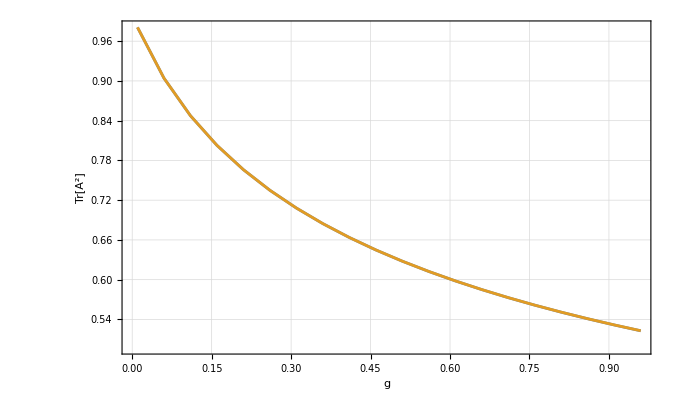

```mathematica
ListLinePlot[{ptsUpper,ptsLower},
Filling->{1->{{2},LightGreen}},
Frame->True,FrameLabel->{"g","Tr[A^2]"},
GridLines->Automatic
]
```

### 导出

```mathematica
(*Export["data/Lambda"~~ToString[Λ]~~"Upper.wdx",ptsUpper]
Export["data/Lambda"~~ToString[Λ]~~"Lower.wdx",ptsLower]*)
```

## CVXPY

将问题输出到 cvxpy 中，要转换的实际上只有  constrain 和 targetFunc

```mathematica
allConstrains={corMat1,corMat2,corMat3,relaxMat};
allVars =DeleteCases[ Variables[{allConstrains,loopEqs/.quadRule/.h->0/.Equal->List}],g]
target = Table[0,{i,1,Length[allVars]}];target[[1]]=1;
```

{e_2,e_6,e_8,e_9,e_14,e_16,e_17,e_19,e_32,e_34,e_35,e_37,e_40,e_41,e_44,e_46,e_48,e_49,e_50,e_51,e_82,e_84,e_85,e_87,e_90,e_91,e_94,e_96,e_97,e_99,e_102,e_104,e_105,e_108,e_109,e_111,e_114,e_116,e_117,e_118,e_119,e_121,e_124,e_125,e_127,e_130,e_131,e_133,e_232,e_234,e_235,e_237,e_240,e_241,e_244,e_246,e_247,e_249,e_252,e_254,e_255,e_258,e_259,e_261,e_264,e_265,e_268,e_270,e_271,e_274,e_275,e_277,e_280,e_282,e_283,e_285,e_288,e_289,e_292,e_294,e_296,e_298,e_299,e_302,e_303,e_305,e_308,e_309,e_311,e_314,e_315,e_318,e_320,e_321,e_322,e_323,e_325,e_328,e_329,e_332,e_334,e_335,e_338,e_340,e_341,e_344,e_345,e_347,e_350,e_351,e_353,e_358,e_360,e_361,e_363,e_368,e_370,e_371,e_374,e_376,e_377,e_378,e_382,e_384,e_386,e_388,e_389,e_390,e_391,e_393,e_394,e_395,e_400,e_402,e_404,e_405,e_406,e_407,e_408,e_409,e_410,e_411,e_728,e_730,e_731,e_733,e_736,e_737,e_740,e_742,e_743,e_745,e_748,e_750,e_751,e_754,e_755,e_757,e_760,e_761,e_764,e_766,e_767,e_770,e_771,e_773,e_776,e_778,e_779,e_781,e_784,e_785,e_788,e_790,e_791,e_793,e_796,e_798,e_799,e_802,e_803,e_805,e_808,e_810,e_811,e_813,e_816,e_817,e_820,e_822,e_823,e_826,e_827,e_829,e_832,e_833,e_836,e_838,e_839,e_841,e_844,e_846,e_847,e_850,e_851,e_853,e_856,e_858,e_859,e_862,e_863,e_865,e_868,e_870,e_871,e_873,e_876,e_877,e_880,e_882,e_883,e_884,e_885,e_887,e_890,e_891,e_894,e_896,e_897,e_899,e_902,e_904,e_905,e_908,e_909,e_911,e_914,e_915,e_917,e_920,e_921,e_924,e_926,e_927,e_929,e_932,e_934,e_935,e_938,e_939,e_941,e_946,e_948,e_949,e_952,e_953,e_955,e_958,e_960,e_961,e_963,e_966,e_968,e_969,e_971,e_974,e_975,e_977,e_980,e_981,e_984,e_986,e_987,e_988,e_989,e_991,e_994,e_995,e_998,e_1000,e_1001,e_1004,e_1006,e_1007,e_1010,e_1011,e_1013,e_1015,e_1017,e_1020,e_1021,e_1024,e_1026,e_1027,e_1030,e_1032,e_1033,e_1036,e_1037,e_1039,e_1044,e_1046,e_1047,e_1050,e_1051,e_1053,e_1056,e_1057,e_1059,e_1062,e_1063,e_1066,e_1067,e_1070,e_1072,e_1073,e_1076,e_1078,e_1079,e_1082,e_1083,e_1085,e_1088,e_1090,e_1091,e_1094,e_1095,e_1097,e_1100,e_1101,e_1103,e_1106,e_1107,e_1110,e_1112,e_1114,e_1115,e_1118,e_1119,e_1121,e_1124,e_1125,e_1127,e_1130,e_1131,e_1134,e_1136,e_1137,e_1139,e_1144,e_1146,e_1147,e_1150,e_1152,e_1153,e_1154,e_1155,e_1157,e_1162,e_1164,e_1165,e_1168,e_1170,e_1171,e_1172,e_1173,e_1175,e_1178,e_1180,e_1181,e_1182,e_1183,e_1185,e_1188,e_1189,e_1191,e_1194,e_1196,e_1197,e_1200,e_1202,e_1203,e_1204,e_1205,e_1207,e_1208,e_1210,e_1211,e_1212,e_1213,e_1215,e_1218,e_1219,e_1221,e_1226,e_1227,e_1228,e_1229,e_1231,e_1234,e_1235,e_1237,e_1242,e_1245,e_1248,e_1249,e_1251,e_1252,e_1254,e_1255,e_1256,e_1257,e_1259,e_1261,e_1263,e_1267,e_1268,e_1269,e_1271,e_1273,e_1275,e_1280,e_1283,e_1288,e_1290,e_1292,e_1293,e_1294,e_1295,e_1296,e_1297,e_1298,e_1299,e_1301,e_1304,e_1305,e_1307,e_1310,e_1311,e_1313,β_1,β_2,β_3,β_4,β_5,β_6,β_7,β_8,β_9,β_10,β_11,β_12,β_13,β_14,β_15,β_16,β_17,β_18,β_19,β_20,β_21,β_22,β_23,β_24,β_25,β_26,β_27,β_28,β_29,β_30,β_31,β_32,β_33,β_34,β_35,β_36,β_37,β_38}

```mathematica
GenerateTask[target,allVars,allConstrains, loopEqs/.quadRule/.h->0, g,Table[i,{i,0.1,5,1/sep}],10^-6]
```

[Matrix] Phasing Matrices.

[LoopEqs] Phasing LoopEqs.

Exporting...

The Task.json has been created.

Variables in allVars have been renamed.